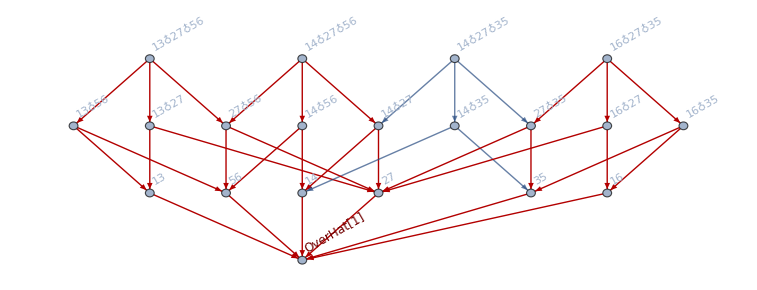

```mathematica
Build[SetP[7],setp7]
```

Building poset setp7  ...

Done

```mathematica
Diagram[setp7]
```

```mathematica
quad1[7]
```

{{{1,6},{2,7},{3,5},{4}},{{1,7},{2,6},{3,5},{4}},{{1,6},{2},{3,5},{4,7}},{{1,7},{2},{3,5},{4,6}},{{1},{2,6},{3,5},{4,7}},{{1},{2,7},{3,5},{4,6}},{{1,6},{2},{3,5,7},{4}},{{1,7},{2},{3,5,6},{4}},{{1,6,7},{2},{3,5},{4}},{{1},{2,6},{3,5,7},{4}},{{1},{2,7},{3,5,6},{4}},{{1},{2,6,7},{3,5},{4}},{{1},{2},{3,5,7},{4,6}},{{1},{2},{3,5,6},{4,7}},{{1},{2},{3,5},{4,6,7}},{{1},{2},{3,5,6,7},{4}}}

```mathematica
MyDistance[{{1,6},{2,7},{3,5},{4}},{{1,6},{2},{3,5,7},{4}}]
```

1

```mathematica
Table[PointerNotation[p1]->p1,{p1,quad1[7]}]
```

{{1,2,3,4,3,1,2}→{{1,6},{2,7},{3,5},{4}},{1,2,3,4,3,2,1}→{{1,7},{2,6},{3,5},{4}},{1,2,3,4,3,1,4}→{{1,6},{2},{3,5},{4,7}},{1,2,3,4,3,4,1}→{{1,7},{2},{3,5},{4,6}},{1,2,3,4,3,2,4}→{{1},{2,6},{3,5},{4,7}},{1,2,3,4,3,4,2}→{{1},{2,7},{3,5},{4,6}},{1,2,3,4,3,1,3}→{{1,6},{2},{3,5,7},{4}},{1,2,3,4,3,3,1}→{{1,7},{2},{3,5,6},{4}},{1,2,3,4,3,1,1}→{{1,6,7},{2},{3,5},{4}},{1,2,3,4,3,2,3}→{{1},{2,6},{3,5,7},{4}},{1,2,3,4,3,3,2}→{{1},{2,7},{3,5,6},{4}},{1,2,3,4,3,2,2}→{{1},{2,6,7},{3,5},{4}},{1,2,3,4,3,4,3}→{{1},{2},{3,5,7},{4,6}},{1,2,3,4,3,3,4}→{{1},{2},{3,5,6},{4,7}},{1,2,3,4,3,4,4}→{{1},{2},{3,5},{4,6,7}},{1,2,3,4,3,3,3}→{{1},{2},{3,5,6,7},{4}}}

```mathematica
Table[MyDistance[p1,{{1,6},{2,7},{3,5},{4}}]->p1,{p1,quad1[7]}]
```

{0→{{1,6},{2,7},{3,5},{4}},2→{{1,7},{2,6},{3,5},{4}},1→{{1,6},{2},{3,5},{4,7}},2→{{1,7},{2},{3,5},{4,6}},2→{{1},{2,6},{3,5},{4,7}},1→{{1},{2,7},{3,5},{4,6}},1→{{1,6},{2},{3,5,7},{4}},2→{{1,7},{2},{3,5,6},{4}},1→{{1,6,7},{2},{3,5},{4}},2→{{1},{2,6},{3,5,7},{4}},1→{{1},{2,7},{3,5,6},{4}},1→{{1},{2,6,7},{3,5},{4}},2→{{1},{2},{3,5,7},{4,6}},2→{{1},{2},{3,5,6},{4,7}},2→{{1},{2},{3,5},{4,6,7}},2→{{1},{2},{3,5,6,7},{4}}}

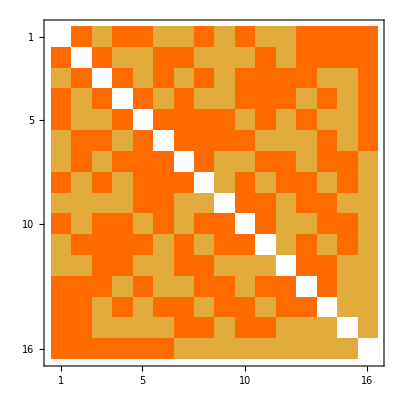

```mathematica
Table[MyDistance[p1,p2],{p1,quad1[7]},{p2,quad1[7]}]//MatrixPlot
```

```mathematica
triangle1[nodes_]:=triangle1[nodes]=Sort[KsetPartitionsWithPattern[nodes,{{1,3},{2,5},{4}}],PartitionValue2[#1]<PartitionValue2[#2]&]
```

```mathematica
triangle2[nodes_]:=triangle2[nodes]=Sort[KsetPartitionsWithPattern[nodes,{{1,4},{2,5},{3}}],PartitionValue2[#1]<PartitionValue2[#2]&]
```

```mathematica
triangle3[nodes_]:=triangle3[nodes]=Sort[KsetPartitionsWithPattern[nodes,{{1,3},{2,4},{5}}],PartitionValue2[#1]<PartitionValue2[#2]&]
```

```mathematica
triangle1[7]
```

{{{1,3},{2,5},{4,7},{6}},{{1,3},{2,5},{4,6},{7}},{{1,3},{2,5},{4},{6,7}},{{1,3,7},{2,5},{4},{6}},{{1,3,6},{2,5},{4},{7}},{{1,3},{2,5,7},{4},{6}},{{1,3},{2,5,6},{4},{7}}}

```mathematica
Table[MyDistance[p1,p2],{p1,triangle1[7]},{p2,triangle1[7]}]//MatrixForm
```

(0 | 1 | 1 | 1 | 1 | 1 | 1
1 | 0 | 1 | 1 | 1 | 1 | 1
1 | 1 | 0 | 1 | 1 | 1 | 1
1 | 1 | 1 | 0 | 1 | 1 | 1
1 | 1 | 1 | 1 | 0 | 1 | 1
1 | 1 | 1 | 1 | 1 | 0 | 1
1 | 1 | 1 | 1 | 1 | 1 | 0)

```mathematica
Table[MeetDistance[setp7,p1,p2],{p1,triangle1[7]},{p2,triangle2[7]}]//MatrixForm
```

(2 | 2 | 2 | 1 | 2 | 2 | 2
2 | 2 | 2 | 2 | 1 | 2 | 2
2 | 2 | 1 | 2 | 2 | 2 | 2
1 | 2 | 2 | 1 | 2 | 2 | 2
2 | 1 | 2 | 2 | 1 | 2 | 2
2 | 2 | 2 | 2 | 2 | 1 | 2
2 | 2 | 2 | 2 | 2 | 2 | 1)

```mathematica
Table[MyDistance[p1,p2],{p1,triangle1[7]},{p2,triangle2[7]}]//MatrixForm
```

(2 | 2 | 2 | 1 | 2 | 2 | 2
2 | 2 | 2 | 2 | 1 | 2 | 2
2 | 2 | 1 | 2 | 2 | 2 | 2
1 | 2 | 2 | 1 | 2 | 2 | 2
2 | 1 | 2 | 2 | 1 | 2 | 2
2 | 2 | 2 | 2 | 2 | 1 | 2
2 | 2 | 2 | 2 | 2 | 2 | 1)

```mathematica
Select[Flatten[Table[{p1,p2},{p1,triangle1[7]},{p2,triangle2[7]}],1],MyDistance[#[[1]],#[[2]]]==1&]
```

{{{{1,3},{2,5},{4,7},{6}},{{1,4,7},{2,5},{3},{6}}},{{{1,3},{2,5},{4,6},{7}},{{1,4,6},{2,5},{3},{7}}},{{{1,3},{2,5},{4},{6,7}},{{1,4},{2,5},{3},{6,7}}},{{{1,3,7},{2,5},{4},{6}},{{1,4},{2,5},{3,7},{6}}},{{{1,3,7},{2,5},{4},{6}},{{1,4,7},{2,5},{3},{6}}},{{{1,3,6},{2,5},{4},{7}},{{1,4},{2,5},{3,6},{7}}},{{{1,3,6},{2,5},{4},{7}},{{1,4,6},{2,5},{3},{7}}},{{{1,3},{2,5,7},{4},{6}},{{1,4},{2,5,7},{3},{6}}},{{{1,3},{2,5,6},{4},{7}},{{1,4},{2,5,6},{3},{7}}}}

```mathematica
Length[Select[Flatten[Table[{p1,p2},{p1,triangle1[7]},{p2,triangle2[7]}],1],MyDistance[#[[1]],#[[2]]]==1&]]
```

9

```mathematica
Length[triangle1[7]]
```

7

```mathematica
TableForm[
Table[
Table[MyDistance[p1,p2],{p1,func2[6]},{p2,func[6]}]//MatrixForm,
{func,{triangle1,triangle2,triangle3}},
{func2,{quad1,quad2,quad3,quad4,quad5}}
]
]
```

(2
2
2
2) | (1
1
1
1) | (2
2
2
2) | (1
1
1
1) | (2
2
2
2)
(2
2
2
2) | (2
2
2
2) | (1
1
1
1) | (1
1
1
1) | (2
2
2
2)
(2
2
2
2) | (1
1
1
1) | (2
2
2
2) | (2
2
2
2) | (1
1
1
1)

```mathematica
TableForm[
Table[
Table[MyDistance[p1,p2],{p1,func2[7]},{p2,func[7]}]//MatrixForm,
{func,{triangle1,triangle2,triangle3}},
{func2,{quad1,quad2,quad3,quad4,quad5}}
]
]
```

(3 | 3 | 3 | 3 | 2 | 2 | 3
3 | 3 | 3 | 2 | 3 | 3 | 2
2 | 3 | 3 | 3 | 2 | 3 | 3
3 | 2 | 3 | 2 | 3 | 3 | 3
2 | 3 | 3 | 3 | 3 | 3 | 2
3 | 2 | 3 | 3 | 3 | 2 | 3
3 | 3 | 3 | 2 | 2 | 2 | 3
3 | 3 | 3 | 2 | 2 | 3 | 2
3 | 3 | 2 | 2 | 2 | 3 | 3
3 | 3 | 3 | 2 | 3 | 2 | 2
3 | 3 | 3 | 3 | 2 | 2 | 2
3 | 3 | 2 | 3 | 3 | 2 | 2
3 | 2 | 3 | 2 | 3 | 2 | 3
2 | 3 | 3 | 3 | 2 | 3 | 2
2 | 2 | 2 | 3 | 3 | 3 | 3
3 | 3 | 2 | 2 | 2 | 2 | 2) | (1 | 2 | 2 | 2 | 2 | 2 | 1
2 | 1 | 2 | 2 | 2 | 1 | 2
2 | 2 | 2 | 2 | 2 | 1 | 1
2 | 2 | 2 | 2 | 2 | 1 | 1
2 | 1 | 2 | 2 | 2 | 1 | 2
1 | 2 | 2 | 2 | 2 | 2 | 1
2 | 2 | 2 | 1 | 2 | 2 | 1
2 | 2 | 2 | 2 | 1 | 1 | 2
2 | 2 | 1 | 2 | 2 | 1 | 1
1 | 2 | 2 | 2 | 1 | 2 | 2
2 | 1 | 2 | 1 | 2 | 2 | 2
2 | 2 | 2 | 2 | 1 | 1 | 2
2 | 2 | 2 | 1 | 2 | 2 | 1
1 | 1 | 1 | 2 | 2 | 2 | 2
2 | 2 | 1 | 2 | 2 | 1 | 1
2 | 2 | 1 | 1 | 1 | 2 | 2) | (3 | 3 | 3 | 2 | 3 | 3 | 2
3 | 3 | 3 | 3 | 2 | 2 | 3
3 | 3 | 3 | 3 | 3 | 2 | 2
3 | 3 | 3 | 3 | 3 | 2 | 2
3 | 3 | 3 | 3 | 2 | 2 | 3
3 | 3 | 3 | 2 | 3 | 3 | 2
2 | 3 | 3 | 2 | 3 | 3 | 2
3 | 2 | 3 | 3 | 2 | 2 | 3
3 | 3 | 2 | 3 | 3 | 2 | 2
2 | 3 | 3 | 2 | 2 | 3 | 3
3 | 2 | 3 | 2 | 2 | 3 | 3
3 | 3 | 2 | 2 | 2 | 3 | 3
3 | 2 | 3 | 3 | 2 | 2 | 3
2 | 3 | 3 | 2 | 3 | 3 | 2
3 | 3 | 2 | 3 | 3 | 2 | 2
2 | 2 | 2 | 2 | 2 | 3 | 3) | (2 | 2 | 2 | 1 | 1 | 2 | 2
2 | 2 | 2 | 1 | 1 | 2 | 2
1 | 2 | 2 | 2 | 1 | 2 | 2
2 | 1 | 2 | 1 | 2 | 2 | 2
1 | 2 | 2 | 2 | 1 | 2 | 2
2 | 1 | 2 | 1 | 2 | 2 | 2
2 | 2 | 2 | 2 | 1 | 1 | 2
2 | 2 | 2 | 1 | 2 | 2 | 1
2 | 2 | 1 | 1 | 1 | 2 | 2
2 | 2 | 2 | 2 | 1 | 1 | 2
2 | 2 | 2 | 1 | 2 | 2 | 1
2 | 2 | 1 | 1 | 1 | 2 | 2
2 | 1 | 2 | 2 | 2 | 1 | 2
1 | 2 | 2 | 2 | 2 | 2 | 1
1 | 1 | 1 | 2 | 2 | 2 | 2
2 | 2 | 1 | 2 | 2 | 1 | 1) | (3 | 3 | 3 | 2 | 2 | 3 | 3
3 | 3 | 3 | 2 | 2 | 3 | 3
3 | 3 | 3 | 3 | 2 | 2 | 3
3 | 3 | 3 | 2 | 3 | 3 | 2
3 | 3 | 3 | 3 | 2 | 2 | 3
3 | 3 | 3 | 2 | 3 | 3 | 2
2 | 3 | 3 | 3 | 2 | 2 | 3
3 | 2 | 3 | 2 | 3 | 3 | 2
3 | 3 | 2 | 2 | 2 | 3 | 3
2 | 3 | 3 | 3 | 2 | 2 | 3
3 | 2 | 3 | 2 | 3 | 3 | 2
3 | 3 | 2 | 2 | 2 | 3 | 3
3 | 2 | 3 | 3 | 3 | 2 | 2
2 | 3 | 3 | 3 | 3 | 2 | 2
3 | 3 | 2 | 3 | 3 | 2 | 2
2 | 2 | 2 | 3 | 3 | 2 | 2)
(3 | 3 | 3 | 3 | 2 | 2 | 3
3 | 3 | 3 | 2 | 3 | 3 | 2
3 | 3 | 3 | 2 | 2 | 3 | 3
3 | 3 | 3 | 2 | 2 | 3 | 3
3 | 3 | 3 | 2 | 3 | 3 | 2
3 | 3 | 3 | 3 | 2 | 2 | 3
2 | 3 | 3 | 3 | 2 | 2 | 3
3 | 2 | 3 | 2 | 3 | 3 | 2
3 | 3 | 2 | 2 | 2 | 3 | 3
2 | 3 | 3 | 3 | 3 | 2 | 2
3 | 2 | 3 | 3 | 3 | 2 | 2
3 | 3 | 2 | 3 | 3 | 2 | 2
2 | 3 | 3 | 3 | 2 | 2 | 3
3 | 2 | 3 | 2 | 3 | 3 | 2
3 | 3 | 2 | 2 | 2 | 3 | 3
2 | 2 | 2 | 3 | 3 | 2 | 2) | (3 | 3 | 3 | 2 | 3 | 3 | 2
3 | 3 | 3 | 3 | 2 | 2 | 3
3 | 3 | 3 | 3 | 3 | 2 | 2
3 | 3 | 3 | 3 | 3 | 2 | 2
3 | 3 | 3 | 3 | 2 | 2 | 3
3 | 3 | 3 | 2 | 3 | 3 | 2
2 | 3 | 3 | 2 | 3 | 3 | 2
3 | 2 | 3 | 3 | 2 | 2 | 3
3 | 3 | 2 | 3 | 3 | 2 | 2
3 | 2 | 3 | 2 | 2 | 3 | 3
2 | 3 | 3 | 2 | 2 | 3 | 3
3 | 2 | 3 | 3 | 2 | 2 | 3
2 | 3 | 3 | 2 | 3 | 3 | 2
3 | 3 | 2 | 2 | 2 | 3 | 3
3 | 3 | 2 | 3 | 3 | 2 | 2
2 | 2 | 2 | 2 | 2 | 3 | 3) | (1 | 2 | 2 | 2 | 2 | 2 | 1
2 | 1 | 2 | 2 | 2 | 1 | 2
2 | 2 | 2 | 2 | 2 | 1 | 1
2 | 2 | 2 | 2 | 2 | 1 | 1
2 | 1 | 2 | 2 | 2 | 1 | 2
1 | 2 | 2 | 2 | 2 | 2 | 1
2 | 2 | 2 | 1 | 2 | 2 | 1
2 | 2 | 2 | 2 | 1 | 1 | 2
2 | 2 | 1 | 2 | 2 | 1 | 1
2 | 1 | 2 | 1 | 2 | 2 | 2
1 | 2 | 2 | 2 | 1 | 2 | 2
1 | 1 | 1 | 2 | 2 | 2 | 2
2 | 2 | 2 | 2 | 1 | 1 | 2
2 | 2 | 2 | 1 | 2 | 2 | 1
2 | 2 | 1 | 2 | 2 | 1 | 1
2 | 2 | 1 | 1 | 1 | 2 | 2) | (1 | 2 | 2 | 2 | 1 | 2 | 2
2 | 1 | 2 | 1 | 2 | 2 | 2
2 | 2 | 2 | 1 | 1 | 2 | 2
2 | 2 | 2 | 1 | 1 | 2 | 2
2 | 1 | 2 | 1 | 2 | 2 | 2
1 | 2 | 2 | 2 | 1 | 2 | 2
2 | 2 | 2 | 2 | 1 | 1 | 2
2 | 2 | 2 | 1 | 2 | 2 | 1
2 | 2 | 1 | 1 | 1 | 2 | 2
2 | 1 | 2 | 2 | 2 | 1 | 2
1 | 2 | 2 | 2 | 2 | 2 | 1
1 | 1 | 1 | 2 | 2 | 2 | 2
2 | 2 | 2 | 2 | 1 | 1 | 2
2 | 2 | 2 | 1 | 2 | 2 | 1
2 | 2 | 1 | 1 | 1 | 2 | 2
2 | 2 | 1 | 2 | 2 | 1 | 1) | (2 | 3 | 3 | 3 | 2 | 3 | 3
3 | 2 | 3 | 2 | 3 | 3 | 3
3 | 3 | 3 | 3 | 2 | 2 | 3
3 | 3 | 3 | 2 | 3 | 3 | 2
3 | 2 | 3 | 3 | 3 | 2 | 3
2 | 3 | 3 | 3 | 3 | 3 | 2
3 | 3 | 3 | 2 | 2 | 2 | 3
3 | 3 | 3 | 2 | 2 | 3 | 2
3 | 3 | 2 | 2 | 2 | 3 | 3
3 | 2 | 3 | 2 | 3 | 2 | 3
2 | 3 | 3 | 3 | 2 | 3 | 2
2 | 2 | 2 | 3 | 3 | 3 | 3
3 | 3 | 3 | 3 | 2 | 2 | 2
3 | 3 | 3 | 2 | 3 | 2 | 2
3 | 3 | 2 | 3 | 3 | 2 | 2
3 | 3 | 2 | 2 | 2 | 2 | 2)
(3 | 3 | 3 | 3 | 2 | 2 | 3
3 | 3 | 3 | 2 | 3 | 3 | 2
3 | 3 | 3 | 3 | 2 | 2 | 3
3 | 3 | 3 | 2 | 3 | 3 | 2
3 | 3 | 3 | 3 | 3 | 2 | 2
3 | 3 | 3 | 3 | 3 | 2 | 2
2 | 3 | 3 | 2 | 2 | 3 | 3
3 | 2 | 3 | 2 | 2 | 3 | 3
3 | 3 | 2 | 2 | 2 | 3 | 3
2 | 3 | 3 | 2 | 3 | 3 | 2
3 | 2 | 3 | 3 | 2 | 2 | 3
3 | 3 | 2 | 3 | 3 | 2 | 2
2 | 3 | 3 | 2 | 3 | 3 | 2
3 | 2 | 3 | 3 | 2 | 2 | 3
3 | 3 | 2 | 3 | 3 | 2 | 2
2 | 2 | 2 | 2 | 2 | 3 | 3) | (2 | 2 | 2 | 2 | 2 | 1 | 1
2 | 2 | 2 | 2 | 2 | 1 | 1
1 | 2 | 2 | 2 | 2 | 2 | 1
2 | 1 | 2 | 2 | 2 | 1 | 2
1 | 2 | 2 | 2 | 2 | 2 | 1
2 | 1 | 2 | 2 | 2 | 1 | 2
2 | 2 | 2 | 1 | 2 | 2 | 1
2 | 2 | 2 | 2 | 1 | 1 | 2
2 | 2 | 1 | 2 | 2 | 1 | 1
2 | 2 | 2 | 2 | 1 | 1 | 2
2 | 2 | 2 | 1 | 2 | 2 | 1
1 | 2 | 2 | 2 | 1 | 2 | 2
2 | 1 | 2 | 1 | 2 | 2 | 2
2 | 2 | 1 | 2 | 2 | 1 | 1
1 | 1 | 1 | 2 | 2 | 2 | 2
2 | 2 | 1 | 1 | 1 | 2 | 2) | (3 | 3 | 3 | 2 | 3 | 3 | 2
3 | 3 | 3 | 3 | 2 | 2 | 3
2 | 3 | 3 | 3 | 3 | 3 | 2
3 | 2 | 3 | 3 | 3 | 2 | 3
2 | 3 | 3 | 3 | 2 | 3 | 3
3 | 2 | 3 | 2 | 3 | 3 | 3
3 | 3 | 3 | 2 | 3 | 2 | 2
3 | 3 | 3 | 3 | 2 | 2 | 2
3 | 3 | 2 | 3 | 3 | 2 | 2
3 | 3 | 3 | 2 | 2 | 2 | 3
3 | 3 | 3 | 2 | 2 | 3 | 2
3 | 3 | 2 | 2 | 2 | 3 | 3
2 | 3 | 3 | 3 | 2 | 3 | 2
3 | 2 | 3 | 2 | 3 | 2 | 3
2 | 2 | 2 | 3 | 3 | 3 | 3
3 | 3 | 2 | 2 | 2 | 2 | 2) | (3 | 3 | 3 | 2 | 2 | 3 | 3
3 | 3 | 3 | 2 | 2 | 3 | 3
3 | 3 | 3 | 3 | 2 | 2 | 3
3 | 3 | 3 | 2 | 3 | 3 | 2
3 | 3 | 3 | 3 | 2 | 2 | 3
3 | 3 | 3 | 2 | 3 | 3 | 2
2 | 3 | 3 | 3 | 2 | 2 | 3
3 | 2 | 3 | 2 | 3 | 3 | 2
3 | 3 | 2 | 2 | 2 | 3 | 3
2 | 3 | 3 | 3 | 2 | 2 | 3
3 | 2 | 3 | 2 | 3 | 3 | 2
3 | 3 | 2 | 2 | 2 | 3 | 3
2 | 3 | 3 | 3 | 3 | 2 | 2
3 | 2 | 3 | 3 | 3 | 2 | 2
3 | 3 | 2 | 3 | 3 | 2 | 2
2 | 2 | 2 | 3 | 3 | 2 | 2) | (2 | 2 | 2 | 1 | 1 | 2 | 2
2 | 2 | 2 | 1 | 1 | 2 | 2
1 | 2 | 2 | 2 | 1 | 2 | 2
2 | 1 | 2 | 1 | 2 | 2 | 2
1 | 2 | 2 | 2 | 1 | 2 | 2
2 | 1 | 2 | 1 | 2 | 2 | 2
2 | 2 | 2 | 2 | 1 | 1 | 2
2 | 2 | 2 | 1 | 2 | 2 | 1
2 | 2 | 1 | 1 | 1 | 2 | 2
2 | 2 | 2 | 2 | 1 | 1 | 2
2 | 2 | 2 | 1 | 2 | 2 | 1
2 | 2 | 1 | 1 | 1 | 2 | 2
1 | 2 | 2 | 2 | 2 | 2 | 1
2 | 1 | 2 | 2 | 2 | 1 | 2
1 | 1 | 1 | 2 | 2 | 2 | 2
2 | 2 | 1 | 2 | 2 | 1 | 1)

```mathematica
SymbolToSets[allGraphs5[alfa1Key,"colofour"]]
```

{{1,3},{2,4},{5}}

```mathematica
TableForm[
Monitor[
Table[
Table[MyDistance[p1,p2],{p1,func2[8]},{p2,func[8]}]//MatrixForm,
{func,{triangle1,triangle2,triangle3}},
{func2,{quad2,quad3}}
],
{func,func2}
]
]
```

(2 | 3 | 3 | 3 | 3 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 1 | 2 | 3 | 3 | 2 | 1 | 3 | 2 | 2 | 3 | 2 | 2 | 3 | 2 | 2 | 3 | 3 | 2 | 2 | 3 | 3 | 3 | 1 | 2 | 2
3 | 3 | 2 | 3 | 3 | 3 | 3 | 2 | 2 | 3 | 3 | 3 | 2 | 1 | 2 | 1 | 3 | 3 | 2 | 2 | 3 | 2 | 2 | 3 | 3 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 2 | 2 | 1
3 | 2 | 3 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 1 | 2 | 1 | 2 | 2 | 3 | 2 | 2 | 3 | 2 | 3 | 3 | 3 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 2 | 1 | 2
3 | 3 | 2 | 3 | 3 | 3 | 3 | 2 | 2 | 3 | 3 | 3 | 2 | 1 | 2 | 1 | 3 | 3 | 2 | 2 | 3 | 2 | 2 | 3 | 3 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 2 | 2 | 1
3 | 2 | 3 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 1 | 2 | 1 | 2 | 2 | 3 | 2 | 2 | 3 | 2 | 3 | 3 | 3 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 2 | 1 | 2
2 | 3 | 3 | 3 | 3 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 1 | 2 | 3 | 3 | 2 | 1 | 3 | 2 | 2 | 3 | 2 | 2 | 3 | 2 | 2 | 3 | 3 | 2 | 2 | 3 | 3 | 3 | 1 | 2 | 2
3 | 2 | 3 | 1 | 2 | 3 | 3 | 3 | 2 | 2 | 3 | 3 | 3 | 3 | 2 | 3 | 1 | 2 | 2 | 3 | 2 | 3 | 3 | 2 | 3 | 2 | 3 | 3 | 3 | 2 | 1 | 3 | 2 | 2 | 2 | 2 | 3
3 | 2 | 3 | 2 | 1 | 3 | 2 | 3 | 3 | 3 | 3 | 2 | 3 | 3 | 1 | 2 | 2 | 3 | 2 | 3 | 2 | 2 | 3 | 3 | 3 | 3 | 2 | 2 | 1 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 2
2 | 3 | 3 | 3 | 3 | 1 | 2 | 2 | 3 | 3 | 2 | 3 | 2 | 3 | 3 | 3 | 2 | 1 | 3 | 2 | 2 | 3 | 3 | 2 | 3 | 3 | 3 | 2 | 3 | 1 | 2 | 2 | 3 | 2 | 2 | 2 | 3
2 | 3 | 3 | 3 | 2 | 2 | 1 | 3 | 3 | 3 | 3 | 2 | 1 | 2 | 3 | 3 | 3 | 2 | 3 | 2 | 2 | 3 | 2 | 3 | 3 | 2 | 1 | 3 | 2 | 3 | 3 | 2 | 2 | 3 | 2 | 3 | 2
3 | 3 | 2 | 3 | 3 | 2 | 3 | 1 | 2 | 3 | 2 | 3 | 3 | 2 | 2 | 1 | 3 | 3 | 2 | 2 | 3 | 2 | 3 | 3 | 3 | 3 | 3 | 1 | 2 | 2 | 3 | 2 | 3 | 2 | 3 | 2 | 2
3 | 3 | 2 | 2 | 3 | 3 | 3 | 2 | 1 | 2 | 3 | 3 | 2 | 1 | 3 | 2 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 3 | 3 | 1 | 2 | 3 | 3 | 3 | 2 | 3 | 2 | 2 | 2 | 3 | 2
3 | 3 | 3 | 2 | 3 | 3 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 2 | 3 | 3 | 3 | 3 | 2 | 2 | 3 | 1 | 2 | 3 | 3 | 2 | 1 | 3 | 2 | 2 | 1 | 2 | 2
3 | 3 | 3 | 3 | 2 | 3 | 2 | 3 | 3 | 3 | 3 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 1 | 2 | 1 | 3 | 3 | 2 | 2 | 3 | 2 | 2 | 1
3 | 3 | 3 | 3 | 3 | 2 | 3 | 2 | 3 | 3 | 2 | 3 | 3 | 3 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 2 | 3 | 2 | 3 | 3 | 3 | 1 | 2 | 1 | 2 | 2 | 3 | 2 | 2 | 1 | 2
3 | 3 | 3 | 3 | 2 | 3 | 2 | 3 | 3 | 3 | 3 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 1 | 2 | 1 | 3 | 3 | 2 | 2 | 3 | 2 | 2 | 1
3 | 3 | 3 | 3 | 3 | 2 | 3 | 2 | 3 | 3 | 2 | 3 | 3 | 3 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 2 | 3 | 2 | 3 | 3 | 3 | 1 | 2 | 1 | 2 | 2 | 3 | 2 | 2 | 1 | 2
3 | 3 | 3 | 2 | 3 | 3 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 2 | 3 | 3 | 3 | 3 | 2 | 2 | 3 | 1 | 2 | 3 | 3 | 2 | 1 | 3 | 2 | 2 | 1 | 2 | 2
1 | 3 | 3 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 3 | 3 | 1 | 2 | 3 | 3 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 2 | 2 | 2 | 3 | 3 | 1 | 2 | 2
2 | 2 | 2 | 2 | 2 | 3 | 3 | 2 | 2 | 2 | 3 | 3 | 3 | 2 | 1 | 1 | 2 | 3 | 1 | 2 | 2 | 1 | 3 | 3 | 2 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 3 | 3 | 2 | 2 | 2
3 | 1 | 3 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 2 | 3 | 3 | 3 | 1 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 2 | 2 | 2 | 2 | 3 | 2 | 3 | 2 | 1 | 2
2 | 2 | 2 | 3 | 3 | 2 | 2 | 2 | 2 | 3 | 2 | 3 | 1 | 1 | 3 | 2 | 3 | 2 | 2 | 1 | 2 | 3 | 1 | 3 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 2 | 3 | 2 | 2 | 2
2 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 2 | 2 | 3 | 2 | 3 | 1 | 1 | 2 | 2 | 1 | 3 | 3 | 1 | 2 | 3 | 3 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 2 | 2 | 2
3 | 3 | 1 | 3 | 3 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 2 | 1 | 2 | 1 | 3 | 3 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 2 | 2 | 2 | 1
2 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 3 | 3 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 1 | 1 | 1
2 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 3 | 3 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 1 | 1 | 1
3 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 3 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 2 | 3 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 2 | 3 | 1 | 1 | 1
3 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 3 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 2 | 3 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 2 | 3 | 1 | 1 | 1
3 | 3 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 2 | 1 | 1 | 1
3 | 3 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 2 | 1 | 1 | 1
2 | 3 | 3 | 3 | 2 | 2 | 1 | 3 | 3 | 3 | 3 | 2 | 1 | 2 | 3 | 3 | 3 | 2 | 3 | 2 | 2 | 3 | 2 | 3 | 3 | 2 | 1 | 3 | 2 | 3 | 3 | 2 | 2 | 3 | 2 | 3 | 2
3 | 3 | 2 | 2 | 3 | 3 | 3 | 2 | 1 | 2 | 3 | 3 | 2 | 1 | 3 | 2 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 3 | 3 | 1 | 2 | 3 | 3 | 3 | 2 | 3 | 2 | 2 | 2 | 3 | 2
3 | 2 | 3 | 2 | 1 | 3 | 2 | 3 | 3 | 3 | 3 | 2 | 3 | 3 | 1 | 2 | 2 | 3 | 2 | 3 | 2 | 2 | 3 | 3 | 3 | 3 | 2 | 2 | 1 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 2
3 | 3 | 2 | 3 | 3 | 2 | 3 | 1 | 2 | 3 | 2 | 3 | 3 | 2 | 2 | 1 | 3 | 3 | 2 | 2 | 3 | 2 | 3 | 3 | 3 | 3 | 3 | 1 | 2 | 2 | 3 | 2 | 3 | 2 | 3 | 2 | 2
3 | 2 | 3 | 1 | 2 | 3 | 3 | 3 | 2 | 2 | 3 | 3 | 3 | 3 | 2 | 3 | 1 | 2 | 2 | 3 | 2 | 3 | 3 | 2 | 3 | 2 | 3 | 3 | 3 | 2 | 1 | 3 | 2 | 2 | 2 | 2 | 3
2 | 3 | 3 | 3 | 3 | 1 | 2 | 2 | 3 | 3 | 2 | 3 | 2 | 3 | 3 | 3 | 2 | 1 | 3 | 2 | 2 | 3 | 3 | 2 | 3 | 3 | 3 | 2 | 3 | 1 | 2 | 2 | 3 | 2 | 2 | 2 | 3
2 | 2 | 2 | 2 | 2 | 3 | 3 | 2 | 2 | 2 | 3 | 3 | 3 | 2 | 1 | 1 | 2 | 3 | 1 | 2 | 2 | 1 | 3 | 3 | 2 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 3 | 3 | 2 | 2 | 2
1 | 3 | 3 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 3 | 3 | 1 | 2 | 3 | 3 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 2 | 2 | 2 | 3 | 3 | 1 | 2 | 2
2 | 2 | 2 | 3 | 3 | 2 | 2 | 2 | 2 | 3 | 2 | 3 | 1 | 1 | 3 | 2 | 3 | 2 | 2 | 1 | 2 | 3 | 1 | 3 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 2 | 3 | 2 | 2 | 2
3 | 1 | 3 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 2 | 3 | 3 | 3 | 1 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 2 | 2 | 2 | 2 | 3 | 2 | 3 | 2 | 1 | 2
3 | 3 | 1 | 3 | 3 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 2 | 1 | 2 | 1 | 3 | 3 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 2 | 2 | 2 | 1
2 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 2 | 2 | 3 | 2 | 3 | 1 | 1 | 2 | 2 | 1 | 3 | 3 | 1 | 2 | 3 | 3 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 2 | 2 | 2
2 | 3 | 3 | 2 | 3 | 3 | 3 | 3 | 2 | 1 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 2 | 2 | 3 | 3 | 2 | 2 | 2 | 2 | 1 | 2 | 3 | 3 | 2 | 1 | 2 | 2 | 2 | 1 | 2 | 2
3 | 2 | 3 | 3 | 3 | 2 | 3 | 2 | 3 | 3 | 1 | 3 | 3 | 3 | 2 | 2 | 2 | 2 | 3 | 2 | 3 | 2 | 2 | 2 | 2 | 3 | 3 | 1 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 1 | 2
3 | 3 | 2 | 3 | 2 | 3 | 2 | 3 | 3 | 3 | 3 | 1 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 2 | 1 | 3 | 3 | 2 | 2 | 2 | 2 | 2 | 1
2 | 2 | 2 | 1 | 2 | 3 | 3 | 2 | 1 | 1 | 3 | 3 | 3 | 2 | 2 | 2 | 2 | 3 | 1 | 2 | 2 | 2 | 3 | 3 | 2 | 2 | 3 | 3 | 3 | 3 | 2 | 2 | 2 | 2 | 2 | 3 | 3
2 | 2 | 2 | 3 | 3 | 1 | 2 | 1 | 2 | 3 | 1 | 3 | 2 | 2 | 3 | 2 | 3 | 2 | 2 | 1 | 2 | 3 | 2 | 3 | 2 | 3 | 3 | 2 | 3 | 2 | 3 | 2 | 2 | 2 | 3 | 2 | 3
2 | 2 | 2 | 2 | 1 | 2 | 1 | 3 | 3 | 3 | 3 | 1 | 2 | 3 | 2 | 3 | 2 | 2 | 2 | 2 | 1 | 3 | 3 | 2 | 2 | 3 | 2 | 3 | 2 | 3 | 3 | 2 | 2 | 2 | 3 | 3 | 2
2 | 3 | 3 | 2 | 3 | 3 | 3 | 3 | 2 | 1 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 2 | 2 | 3 | 3 | 2 | 2 | 2 | 2 | 1 | 2 | 3 | 3 | 2 | 1 | 2 | 2 | 2 | 1 | 2 | 2
3 | 2 | 3 | 3 | 3 | 2 | 3 | 2 | 3 | 3 | 1 | 3 | 3 | 3 | 2 | 2 | 2 | 2 | 3 | 2 | 3 | 2 | 2 | 2 | 2 | 3 | 3 | 1 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 1 | 2
3 | 3 | 2 | 3 | 2 | 3 | 2 | 3 | 3 | 3 | 3 | 1 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 2 | 1 | 3 | 3 | 2 | 2 | 2 | 2 | 2 | 1
2 | 3 | 3 | 3 | 2 | 2 | 2 | 2 | 3 | 2 | 2 | 2 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 3 | 3 | 1 | 3 | 3 | 2 | 3 | 2 | 1 | 1 | 2 | 3 | 1 | 2 | 2 | 2 | 2 | 2
3 | 2 | 3 | 2 | 2 | 3 | 2 | 3 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 2 | 3 | 3 | 1 | 3 | 2 | 1 | 1 | 3 | 2 | 3 | 2 | 2 | 1 | 2 | 2 | 2 | 2
3 | 3 | 2 | 2 | 3 | 2 | 3 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 3 | 3 | 1 | 2 | 2 | 3 | 2 | 3 | 1 | 1 | 2 | 2 | 1 | 2 | 2 | 2
2 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1 | 1 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1 | 1
1 | 3 | 3 | 3 | 2 | 1 | 1 | 2 | 3 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 2 | 3 | 2 | 2 | 2 | 2 | 3 | 1 | 2 | 2 | 2 | 3 | 3
3 | 1 | 3 | 1 | 1 | 3 | 2 | 3 | 2 | 2 | 2 | 2 | 3 | 3 | 2 | 3 | 2 | 3 | 2 | 2 | 2 | 3 | 2 | 3 | 2 | 2 | 2 | 3 | 2 | 3 | 2 | 2 | 1 | 2 | 3 | 2 | 3
3 | 3 | 1 | 2 | 3 | 2 | 3 | 1 | 1 | 2 | 2 | 2 | 3 | 2 | 3 | 2 | 3 | 3 | 2 | 2 | 2 | 3 | 3 | 2 | 2 | 2 | 3 | 2 | 3 | 2 | 2 | 2 | 2 | 1 | 3 | 3 | 2
2 | 3 | 3 | 3 | 2 | 2 | 2 | 2 | 3 | 2 | 2 | 2 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 3 | 3 | 1 | 3 | 3 | 2 | 3 | 2 | 1 | 1 | 2 | 3 | 1 | 2 | 2 | 2 | 2 | 2
3 | 2 | 3 | 2 | 2 | 3 | 2 | 3 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 2 | 3 | 3 | 1 | 3 | 2 | 1 | 1 | 3 | 2 | 3 | 2 | 2 | 1 | 2 | 2 | 2 | 2
3 | 3 | 2 | 2 | 3 | 2 | 3 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 3 | 3 | 1 | 2 | 2 | 3 | 2 | 3 | 1 | 1 | 2 | 2 | 1 | 2 | 2 | 2
1 | 1 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1 | 1 | 2 | 2 | 2 | 1 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 2 | 2 | 2 | 2 | 2
2 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1 | 1 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1 | 1
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1 | 1 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1 | 1 | 2 | 2 | 2) | (4 | 4 | 4 | 3 | 4 | 4 | 4 | 4 | 3 | 3 | 4 | 4 | 3 | 3 | 4 | 4 | 3 | 3 | 4 | 4 | 4 | 4 | 3 | 3 | 4 | 2 | 3 | 4 | 4 | 3 | 2 | 4 | 3 | 3 | 2 | 3 | 3
4 | 4 | 4 | 4 | 3 | 4 | 3 | 4 | 4 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 4 | 4 | 4 | 3 | 3 | 4 | 4 | 3 | 2 | 3 | 2 | 4 | 4 | 3 | 3 | 4 | 3 | 3 | 2
4 | 4 | 4 | 4 | 4 | 3 | 4 | 3 | 4 | 4 | 3 | 4 | 4 | 4 | 3 | 3 | 3 | 3 | 4 | 4 | 4 | 3 | 4 | 3 | 4 | 4 | 4 | 2 | 3 | 2 | 3 | 3 | 4 | 3 | 3 | 2 | 3
4 | 4 | 4 | 4 | 3 | 4 | 3 | 4 | 4 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 4 | 4 | 4 | 3 | 3 | 4 | 4 | 3 | 2 | 3 | 2 | 4 | 4 | 3 | 3 | 4 | 3 | 3 | 2
4 | 4 | 4 | 4 | 4 | 3 | 4 | 3 | 4 | 4 | 3 | 4 | 4 | 4 | 3 | 3 | 3 | 3 | 4 | 4 | 4 | 3 | 4 | 3 | 4 | 4 | 4 | 2 | 3 | 2 | 3 | 3 | 4 | 3 | 3 | 2 | 3
4 | 4 | 4 | 3 | 4 | 4 | 4 | 4 | 3 | 3 | 4 | 4 | 3 | 3 | 4 | 4 | 3 | 3 | 4 | 4 | 4 | 4 | 3 | 3 | 4 | 2 | 3 | 4 | 4 | 3 | 2 | 4 | 3 | 3 | 2 | 3 | 3
4 | 3 | 4 | 2 | 3 | 3 | 4 | 3 | 3 | 3 | 3 | 4 | 4 | 4 | 3 | 4 | 2 | 3 | 3 | 4 | 3 | 4 | 4 | 3 | 4 | 3 | 4 | 3 | 4 | 2 | 2 | 3 | 3 | 2 | 3 | 3 | 4
4 | 3 | 4 | 3 | 2 | 3 | 3 | 3 | 4 | 4 | 3 | 3 | 4 | 4 | 2 | 3 | 3 | 4 | 3 | 4 | 3 | 3 | 4 | 4 | 4 | 4 | 3 | 2 | 2 | 3 | 4 | 2 | 3 | 3 | 4 | 3 | 3
3 | 4 | 4 | 3 | 4 | 2 | 3 | 3 | 3 | 3 | 3 | 4 | 3 | 4 | 4 | 4 | 3 | 2 | 4 | 3 | 3 | 4 | 4 | 3 | 4 | 3 | 4 | 3 | 4 | 2 | 2 | 3 | 3 | 2 | 3 | 3 | 4
3 | 4 | 4 | 3 | 3 | 3 | 2 | 4 | 3 | 3 | 4 | 3 | 2 | 3 | 4 | 4 | 4 | 3 | 4 | 3 | 3 | 4 | 3 | 4 | 4 | 2 | 2 | 4 | 3 | 4 | 3 | 3 | 2 | 3 | 3 | 4 | 3
4 | 4 | 3 | 4 | 3 | 3 | 3 | 2 | 3 | 4 | 3 | 3 | 4 | 3 | 3 | 2 | 4 | 4 | 3 | 3 | 4 | 3 | 4 | 4 | 4 | 4 | 3 | 2 | 2 | 3 | 4 | 2 | 3 | 3 | 4 | 3 | 3
4 | 4 | 3 | 3 | 3 | 4 | 3 | 3 | 2 | 3 | 4 | 3 | 3 | 2 | 4 | 3 | 4 | 4 | 3 | 3 | 4 | 4 | 3 | 4 | 4 | 2 | 2 | 4 | 3 | 4 | 3 | 3 | 2 | 3 | 3 | 4 | 3
3 | 4 | 4 | 3 | 4 | 4 | 4 | 4 | 3 | 2 | 4 | 4 | 3 | 3 | 4 | 4 | 3 | 3 | 3 | 4 | 4 | 3 | 3 | 3 | 3 | 2 | 3 | 4 | 4 | 3 | 2 | 3 | 3 | 3 | 2 | 3 | 3
3 | 4 | 4 | 4 | 3 | 3 | 3 | 3 | 4 | 3 | 3 | 3 | 4 | 4 | 3 | 3 | 4 | 4 | 3 | 4 | 4 | 2 | 4 | 4 | 3 | 4 | 3 | 2 | 2 | 3 | 4 | 2 | 3 | 3 | 3 | 3 | 3
4 | 3 | 4 | 4 | 4 | 3 | 4 | 3 | 4 | 4 | 2 | 4 | 4 | 4 | 3 | 3 | 3 | 3 | 4 | 3 | 4 | 3 | 3 | 3 | 3 | 4 | 4 | 2 | 3 | 2 | 3 | 3 | 3 | 3 | 3 | 2 | 3
4 | 3 | 4 | 3 | 3 | 4 | 3 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 4 | 4 | 4 | 3 | 4 | 4 | 2 | 4 | 3 | 2 | 2 | 4 | 3 | 4 | 3 | 3 | 2 | 3 | 3 | 3 | 3
4 | 4 | 3 | 3 | 4 | 3 | 4 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 4 | 4 | 3 | 3 | 4 | 4 | 3 | 4 | 4 | 2 | 3 | 3 | 4 | 3 | 4 | 2 | 2 | 3 | 3 | 2 | 3 | 3 | 3
4 | 4 | 3 | 4 | 3 | 4 | 3 | 4 | 4 | 4 | 4 | 2 | 3 | 3 | 3 | 3 | 4 | 4 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 3 | 2 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 2
3 | 4 | 4 | 3 | 4 | 3 | 3 | 4 | 3 | 3 | 4 | 4 | 2 | 3 | 4 | 4 | 3 | 2 | 4 | 3 | 3 | 4 | 3 | 3 | 4 | 2 | 3 | 4 | 4 | 3 | 2 | 4 | 3 | 3 | 2 | 3 | 3
4 | 4 | 3 | 4 | 3 | 4 | 3 | 3 | 3 | 4 | 4 | 3 | 3 | 2 | 3 | 2 | 4 | 4 | 3 | 3 | 4 | 3 | 3 | 4 | 4 | 3 | 2 | 3 | 2 | 4 | 4 | 3 | 3 | 4 | 3 | 3 | 2
4 | 3 | 4 | 3 | 3 | 3 | 4 | 3 | 4 | 4 | 3 | 4 | 4 | 4 | 2 | 3 | 2 | 3 | 3 | 4 | 3 | 3 | 4 | 3 | 4 | 4 | 4 | 2 | 3 | 2 | 3 | 3 | 4 | 3 | 3 | 2 | 3
4 | 4 | 3 | 4 | 3 | 4 | 3 | 3 | 3 | 4 | 4 | 3 | 3 | 2 | 3 | 2 | 4 | 4 | 3 | 3 | 4 | 3 | 3 | 4 | 4 | 3 | 2 | 3 | 2 | 4 | 4 | 3 | 3 | 4 | 3 | 3 | 2
4 | 3 | 4 | 3 | 3 | 3 | 4 | 3 | 4 | 4 | 3 | 4 | 4 | 4 | 2 | 3 | 2 | 3 | 3 | 4 | 3 | 3 | 4 | 3 | 4 | 4 | 4 | 2 | 3 | 2 | 3 | 3 | 4 | 3 | 3 | 2 | 3
3 | 4 | 4 | 3 | 4 | 3 | 3 | 4 | 3 | 3 | 4 | 4 | 2 | 3 | 4 | 4 | 3 | 2 | 4 | 3 | 3 | 4 | 3 | 3 | 4 | 2 | 3 | 4 | 4 | 3 | 2 | 4 | 3 | 3 | 2 | 3 | 3
3 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 3 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 2 | 2 | 2
3 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 3 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 2 | 2 | 2
4 | 3 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 3 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 3 | 4 | 3 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 3 | 4 | 2 | 2 | 2
4 | 3 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 3 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 3 | 4 | 3 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 3 | 4 | 2 | 2 | 2
4 | 4 | 3 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 3 | 3 | 3 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 3 | 2 | 2 | 2
4 | 4 | 3 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 3 | 3 | 3 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 3 | 2 | 2 | 2
3 | 4 | 4 | 3 | 3 | 3 | 2 | 4 | 3 | 3 | 4 | 3 | 2 | 3 | 4 | 4 | 4 | 3 | 4 | 3 | 3 | 4 | 3 | 4 | 4 | 2 | 2 | 4 | 3 | 4 | 3 | 3 | 2 | 3 | 3 | 4 | 3
4 | 4 | 3 | 3 | 3 | 4 | 3 | 3 | 2 | 3 | 4 | 3 | 3 | 2 | 4 | 3 | 4 | 4 | 3 | 3 | 4 | 4 | 3 | 4 | 4 | 2 | 2 | 4 | 3 | 4 | 3 | 3 | 2 | 3 | 3 | 4 | 3
4 | 3 | 4 | 3 | 2 | 3 | 3 | 3 | 4 | 4 | 3 | 3 | 4 | 4 | 2 | 3 | 3 | 4 | 3 | 4 | 3 | 3 | 4 | 4 | 4 | 4 | 3 | 2 | 2 | 3 | 4 | 2 | 3 | 3 | 4 | 3 | 3
4 | 4 | 3 | 4 | 3 | 3 | 3 | 2 | 3 | 4 | 3 | 3 | 4 | 3 | 3 | 2 | 4 | 4 | 3 | 3 | 4 | 3 | 4 | 4 | 4 | 4 | 3 | 2 | 2 | 3 | 4 | 2 | 3 | 3 | 4 | 3 | 3
4 | 3 | 4 | 2 | 3 | 3 | 4 | 3 | 3 | 3 | 3 | 4 | 4 | 4 | 3 | 4 | 2 | 3 | 3 | 4 | 3 | 4 | 4 | 3 | 4 | 3 | 4 | 3 | 4 | 2 | 2 | 3 | 3 | 2 | 3 | 3 | 4
3 | 4 | 4 | 3 | 4 | 2 | 3 | 3 | 3 | 3 | 3 | 4 | 3 | 4 | 4 | 4 | 3 | 2 | 4 | 3 | 3 | 4 | 4 | 3 | 4 | 3 | 4 | 3 | 4 | 2 | 2 | 3 | 3 | 2 | 3 | 3 | 4
3 | 4 | 4 | 4 | 3 | 3 | 3 | 3 | 4 | 3 | 3 | 3 | 4 | 4 | 3 | 3 | 4 | 4 | 3 | 4 | 4 | 2 | 4 | 4 | 3 | 4 | 3 | 2 | 2 | 3 | 4 | 2 | 3 | 3 | 3 | 3 | 3
3 | 4 | 4 | 3 | 4 | 4 | 4 | 4 | 3 | 2 | 4 | 4 | 3 | 3 | 4 | 4 | 3 | 3 | 3 | 4 | 4 | 3 | 3 | 3 | 3 | 2 | 3 | 4 | 4 | 3 | 2 | 3 | 3 | 3 | 2 | 3 | 3
4 | 3 | 4 | 3 | 3 | 4 | 3 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 4 | 4 | 4 | 3 | 4 | 4 | 2 | 4 | 3 | 2 | 2 | 4 | 3 | 4 | 3 | 3 | 2 | 3 | 3 | 3 | 3
4 | 3 | 4 | 4 | 4 | 3 | 4 | 3 | 4 | 4 | 2 | 4 | 4 | 4 | 3 | 3 | 3 | 3 | 4 | 3 | 4 | 3 | 3 | 3 | 3 | 4 | 4 | 2 | 3 | 2 | 3 | 3 | 3 | 3 | 3 | 2 | 3
4 | 4 | 3 | 4 | 3 | 4 | 3 | 4 | 4 | 4 | 4 | 2 | 3 | 3 | 3 | 3 | 4 | 4 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 3 | 2 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 2
4 | 4 | 3 | 3 | 4 | 3 | 4 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 4 | 4 | 3 | 3 | 4 | 4 | 3 | 4 | 4 | 2 | 3 | 3 | 4 | 3 | 4 | 2 | 2 | 3 | 3 | 2 | 3 | 3 | 3
2 | 4 | 4 | 3 | 4 | 3 | 3 | 4 | 3 | 2 | 4 | 4 | 2 | 3 | 4 | 4 | 3 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 3 | 4 | 4 | 3 | 2 | 3 | 3 | 3 | 2 | 3 | 3
4 | 2 | 4 | 3 | 3 | 3 | 4 | 3 | 4 | 4 | 2 | 4 | 4 | 4 | 2 | 3 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 2 | 3 | 2 | 3 | 3 | 3 | 3 | 3 | 2 | 3
4 | 4 | 2 | 4 | 3 | 4 | 3 | 3 | 3 | 4 | 4 | 2 | 3 | 2 | 3 | 2 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 3 | 2 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 2
2 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 3 | 3 | 3 | 4 | 4 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 2 | 2 | 3 | 4 | 4
4 | 2 | 4 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 2 | 3 | 4 | 4 | 3 | 4 | 3 | 4 | 3 | 3 | 3 | 4 | 3 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 2 | 2 | 4 | 3 | 4
4 | 4 | 2 | 3 | 3 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 4 | 3 | 4 | 3 | 4 | 4 | 3 | 3 | 3 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 2 | 2 | 4 | 4 | 3
2 | 4 | 4 | 3 | 4 | 3 | 3 | 4 | 3 | 2 | 4 | 4 | 2 | 3 | 4 | 4 | 3 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 3 | 4 | 4 | 3 | 2 | 3 | 3 | 3 | 2 | 3 | 3
4 | 2 | 4 | 3 | 3 | 3 | 4 | 3 | 4 | 4 | 2 | 4 | 4 | 4 | 2 | 3 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 2 | 3 | 2 | 3 | 3 | 3 | 3 | 3 | 2 | 3
4 | 4 | 2 | 4 | 3 | 4 | 3 | 3 | 3 | 4 | 4 | 2 | 3 | 2 | 3 | 2 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 3 | 2 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 2
3 | 3 | 3 | 3 | 2 | 3 | 3 | 2 | 3 | 3 | 3 | 3 | 4 | 3 | 2 | 2 | 3 | 4 | 2 | 3 | 3 | 2 | 4 | 4 | 3 | 4 | 3 | 2 | 2 | 3 | 4 | 2 | 3 | 3 | 3 | 3 | 3
3 | 3 | 3 | 3 | 3 | 3 | 2 | 3 | 2 | 3 | 3 | 3 | 2 | 2 | 4 | 3 | 4 | 3 | 3 | 2 | 3 | 4 | 2 | 4 | 3 | 2 | 2 | 4 | 3 | 4 | 3 | 3 | 2 | 3 | 3 | 3 | 3
3 | 3 | 3 | 2 | 3 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 3 | 4 | 2 | 2 | 3 | 3 | 2 | 4 | 4 | 2 | 3 | 3 | 4 | 3 | 4 | 2 | 2 | 3 | 3 | 2 | 3 | 3 | 3
3 | 3 | 3 | 4 | 4 | 4 | 4 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 2 | 2
3 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 2 | 2 | 3 | 3 | 4 | 3 | 3 | 3 | 3 | 4 | 2 | 3 | 3 | 3 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 2 | 2 | 3 | 4 | 4
3 | 3 | 3 | 3 | 3 | 2 | 2 | 2 | 2 | 3 | 2 | 3 | 3 | 3 | 4 | 3 | 4 | 3 | 3 | 2 | 3 | 4 | 3 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 2 | 2 | 4 | 3 | 4
3 | 3 | 3 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 2 | 3 | 4 | 3 | 4 | 3 | 3 | 3 | 3 | 2 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 2 | 2 | 4 | 4 | 3
3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 2 | 2 | 4 | 4 | 4 | 4 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 2 | 2 | 3 | 3 | 3
3 | 3 | 3 | 3 | 2 | 3 | 3 | 2 | 3 | 3 | 3 | 3 | 4 | 3 | 2 | 2 | 3 | 4 | 2 | 3 | 3 | 2 | 4 | 4 | 3 | 4 | 3 | 2 | 2 | 3 | 4 | 2 | 3 | 3 | 3 | 3 | 3
3 | 3 | 3 | 3 | 3 | 3 | 2 | 3 | 2 | 3 | 3 | 3 | 2 | 2 | 4 | 3 | 4 | 3 | 3 | 2 | 3 | 4 | 2 | 4 | 3 | 2 | 2 | 4 | 3 | 4 | 3 | 3 | 2 | 3 | 3 | 3 | 3
3 | 3 | 3 | 2 | 3 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 3 | 4 | 2 | 2 | 3 | 3 | 2 | 4 | 4 | 2 | 3 | 3 | 4 | 3 | 4 | 2 | 2 | 3 | 3 | 2 | 3 | 3 | 3
3 | 3 | 3 | 4 | 4 | 4 | 4 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 2 | 2
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 2 | 2 | 3 | 3 | 3 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 2 | 2 | 3 | 3 | 3)
(4 | 4 | 4 | 4 | 4 | 3 | 3 | 4 | 4 | 3 | 3 | 4 | 4 | 3 | 3 | 4 | 4 | 4 | 3 | 4 | 4 | 4 | 3 | 3 | 4 | 2 | 3 | 4 | 4 | 3 | 2 | 4 | 3 | 3 | 2 | 3 | 3
4 | 4 | 4 | 4 | 4 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 3 | 3 | 3 | 4 | 4 | 3 | 2 | 3 | 2 | 4 | 4 | 3 | 3 | 4 | 3 | 3 | 2
4 | 4 | 4 | 3 | 3 | 4 | 4 | 4 | 4 | 4 | 4 | 3 | 3 | 3 | 3 | 4 | 4 | 4 | 4 | 3 | 4 | 3 | 4 | 3 | 4 | 4 | 4 | 2 | 3 | 2 | 3 | 3 | 4 | 3 | 3 | 2 | 3
4 | 4 | 4 | 4 | 4 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 3 | 3 | 3 | 4 | 4 | 3 | 2 | 3 | 2 | 4 | 4 | 3 | 3 | 4 | 3 | 3 | 2
4 | 4 | 4 | 3 | 3 | 4 | 4 | 4 | 4 | 4 | 4 | 3 | 3 | 3 | 3 | 4 | 4 | 4 | 4 | 3 | 4 | 3 | 4 | 3 | 4 | 4 | 4 | 2 | 3 | 2 | 3 | 3 | 4 | 3 | 3 | 2 | 3
4 | 4 | 4 | 4 | 4 | 3 | 3 | 4 | 4 | 3 | 3 | 4 | 4 | 3 | 3 | 4 | 4 | 4 | 3 | 4 | 4 | 4 | 3 | 3 | 4 | 2 | 3 | 4 | 4 | 3 | 2 | 4 | 3 | 3 | 2 | 3 | 3
3 | 4 | 4 | 2 | 3 | 3 | 3 | 4 | 3 | 3 | 4 | 4 | 4 | 3 | 2 | 4 | 3 | 3 | 3 | 3 | 4 | 4 | 4 | 3 | 4 | 3 | 4 | 3 | 4 | 2 | 2 | 3 | 3 | 2 | 3 | 3 | 4
4 | 4 | 3 | 3 | 2 | 4 | 3 | 3 | 3 | 4 | 3 | 3 | 2 | 4 | 4 | 3 | 3 | 4 | 4 | 3 | 3 | 3 | 4 | 4 | 4 | 4 | 3 | 2 | 2 | 3 | 4 | 2 | 3 | 3 | 4 | 3 | 3
4 | 3 | 4 | 3 | 3 | 2 | 3 | 3 | 4 | 4 | 4 | 3 | 4 | 2 | 3 | 3 | 4 | 3 | 3 | 3 | 4 | 4 | 4 | 3 | 4 | 3 | 4 | 3 | 4 | 2 | 2 | 3 | 3 | 2 | 3 | 3 | 4
4 | 4 | 3 | 4 | 3 | 3 | 2 | 3 | 3 | 3 | 2 | 4 | 3 | 4 | 4 | 3 | 3 | 4 | 3 | 4 | 3 | 4 | 3 | 4 | 4 | 2 | 2 | 4 | 3 | 4 | 3 | 3 | 2 | 3 | 3 | 4 | 3
4 | 3 | 4 | 3 | 3 | 3 | 4 | 2 | 3 | 4 | 4 | 2 | 3 | 3 | 4 | 3 | 4 | 3 | 4 | 3 | 3 | 3 | 4 | 4 | 4 | 4 | 3 | 2 | 2 | 3 | 4 | 2 | 3 | 3 | 4 | 3 | 3
3 | 4 | 4 | 3 | 4 | 3 | 3 | 3 | 2 | 2 | 3 | 4 | 4 | 4 | 3 | 4 | 3 | 3 | 3 | 4 | 3 | 4 | 3 | 4 | 4 | 2 | 2 | 4 | 3 | 4 | 3 | 3 | 2 | 3 | 3 | 4 | 3
3 | 4 | 4 | 3 | 4 | 3 | 3 | 4 | 3 | 2 | 3 | 4 | 4 | 3 | 2 | 4 | 3 | 3 | 3 | 4 | 4 | 4 | 3 | 3 | 4 | 2 | 3 | 4 | 4 | 3 | 2 | 4 | 3 | 3 | 2 | 3 | 3
4 | 4 | 3 | 4 | 3 | 4 | 3 | 3 | 3 | 3 | 2 | 3 | 2 | 4 | 4 | 3 | 3 | 4 | 4 | 4 | 3 | 3 | 3 | 4 | 4 | 3 | 2 | 3 | 2 | 4 | 4 | 3 | 3 | 4 | 3 | 3 | 2
4 | 3 | 4 | 3 | 3 | 3 | 4 | 3 | 4 | 4 | 4 | 2 | 3 | 2 | 3 | 3 | 4 | 3 | 4 | 3 | 4 | 3 | 4 | 3 | 4 | 4 | 4 | 2 | 3 | 2 | 3 | 3 | 4 | 3 | 3 | 2 | 3
4 | 4 | 3 | 4 | 3 | 4 | 3 | 3 | 3 | 3 | 2 | 3 | 2 | 4 | 4 | 3 | 3 | 4 | 4 | 4 | 3 | 3 | 3 | 4 | 4 | 3 | 2 | 3 | 2 | 4 | 4 | 3 | 3 | 4 | 3 | 3 | 2
4 | 3 | 4 | 3 | 3 | 3 | 4 | 3 | 4 | 4 | 4 | 2 | 3 | 2 | 3 | 3 | 4 | 3 | 4 | 3 | 4 | 3 | 4 | 3 | 4 | 4 | 4 | 2 | 3 | 2 | 3 | 3 | 4 | 3 | 3 | 2 | 3
3 | 4 | 4 | 3 | 4 | 3 | 3 | 4 | 3 | 2 | 3 | 4 | 4 | 3 | 2 | 4 | 3 | 3 | 3 | 4 | 4 | 4 | 3 | 3 | 4 | 2 | 3 | 4 | 4 | 3 | 2 | 4 | 3 | 3 | 2 | 3 | 3
3 | 4 | 4 | 4 | 4 | 3 | 3 | 4 | 4 | 3 | 3 | 4 | 4 | 3 | 3 | 3 | 4 | 4 | 2 | 4 | 4 | 3 | 3 | 3 | 3 | 2 | 3 | 4 | 4 | 3 | 2 | 3 | 3 | 3 | 2 | 3 | 3
3 | 4 | 4 | 3 | 3 | 4 | 4 | 3 | 3 | 4 | 4 | 3 | 3 | 4 | 4 | 3 | 4 | 4 | 3 | 3 | 3 | 2 | 4 | 4 | 3 | 4 | 3 | 2 | 2 | 3 | 4 | 2 | 3 | 3 | 3 | 3 | 3
4 | 3 | 4 | 3 | 3 | 4 | 4 | 4 | 4 | 4 | 4 | 3 | 3 | 3 | 3 | 4 | 3 | 4 | 4 | 2 | 4 | 3 | 3 | 3 | 3 | 4 | 4 | 2 | 3 | 2 | 3 | 3 | 3 | 3 | 3 | 2 | 3
4 | 3 | 4 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 4 | 4 | 4 | 3 | 4 | 3 | 3 | 3 | 4 | 2 | 4 | 3 | 2 | 2 | 4 | 3 | 4 | 3 | 3 | 2 | 3 | 3 | 3 | 3
4 | 4 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 4 | 4 | 4 | 4 | 3 | 3 | 4 | 4 | 3 | 3 | 3 | 3 | 4 | 4 | 2 | 3 | 3 | 4 | 3 | 4 | 2 | 2 | 3 | 3 | 2 | 3 | 3 | 3
4 | 4 | 3 | 4 | 4 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 4 | 4 | 3 | 4 | 4 | 2 | 3 | 3 | 3 | 3 | 3 | 2 | 3 | 2 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 2
3 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 3 | 4 | 4 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 2 | 2 | 2
3 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 3 | 4 | 4 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 2 | 2 | 2
4 | 3 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 3 | 4 | 4 | 3 | 4 | 3 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 3 | 4 | 2 | 2 | 2
4 | 3 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 3 | 4 | 4 | 3 | 4 | 3 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 3 | 4 | 2 | 2 | 2
4 | 4 | 3 | 4 | 4 | 4 | 4 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 3 | 4 | 4 | 3 | 3 | 3 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 3 | 2 | 2 | 2
4 | 4 | 3 | 4 | 4 | 4 | 4 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 3 | 4 | 4 | 3 | 3 | 3 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 3 | 2 | 2 | 2
4 | 4 | 3 | 4 | 3 | 3 | 2 | 3 | 3 | 3 | 2 | 4 | 3 | 4 | 4 | 3 | 3 | 4 | 3 | 4 | 3 | 4 | 3 | 4 | 4 | 2 | 2 | 4 | 3 | 4 | 3 | 3 | 2 | 3 | 3 | 4 | 3
3 | 4 | 4 | 3 | 4 | 3 | 3 | 3 | 2 | 2 | 3 | 4 | 4 | 4 | 3 | 4 | 3 | 3 | 3 | 4 | 3 | 4 | 3 | 4 | 4 | 2 | 2 | 4 | 3 | 4 | 3 | 3 | 2 | 3 | 3 | 4 | 3
4 | 4 | 3 | 3 | 2 | 4 | 3 | 3 | 3 | 4 | 3 | 3 | 2 | 4 | 4 | 3 | 3 | 4 | 4 | 3 | 3 | 3 | 4 | 4 | 4 | 4 | 3 | 2 | 2 | 3 | 4 | 2 | 3 | 3 | 4 | 3 | 3
4 | 3 | 4 | 3 | 3 | 3 | 4 | 2 | 3 | 4 | 4 | 2 | 3 | 3 | 4 | 3 | 4 | 3 | 4 | 3 | 3 | 3 | 4 | 4 | 4 | 4 | 3 | 2 | 2 | 3 | 4 | 2 | 3 | 3 | 4 | 3 | 3
3 | 4 | 4 | 2 | 3 | 3 | 3 | 4 | 3 | 3 | 4 | 4 | 4 | 3 | 2 | 4 | 3 | 3 | 3 | 3 | 4 | 4 | 4 | 3 | 4 | 3 | 4 | 3 | 4 | 2 | 2 | 3 | 3 | 2 | 3 | 3 | 4
4 | 3 | 4 | 3 | 3 | 2 | 3 | 3 | 4 | 4 | 4 | 3 | 4 | 2 | 3 | 3 | 4 | 3 | 3 | 3 | 4 | 4 | 4 | 3 | 4 | 3 | 4 | 3 | 4 | 2 | 2 | 3 | 3 | 2 | 3 | 3 | 4
3 | 4 | 4 | 3 | 3 | 4 | 4 | 3 | 3 | 4 | 4 | 3 | 3 | 4 | 4 | 3 | 4 | 4 | 3 | 3 | 3 | 2 | 4 | 4 | 3 | 4 | 3 | 2 | 2 | 3 | 4 | 2 | 3 | 3 | 3 | 3 | 3
3 | 4 | 4 | 4 | 4 | 3 | 3 | 4 | 4 | 3 | 3 | 4 | 4 | 3 | 3 | 3 | 4 | 4 | 2 | 4 | 4 | 3 | 3 | 3 | 3 | 2 | 3 | 4 | 4 | 3 | 2 | 3 | 3 | 3 | 2 | 3 | 3
4 | 3 | 4 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 4 | 4 | 4 | 3 | 4 | 3 | 3 | 3 | 4 | 2 | 4 | 3 | 2 | 2 | 4 | 3 | 4 | 3 | 3 | 2 | 3 | 3 | 3 | 3
4 | 3 | 4 | 3 | 3 | 4 | 4 | 4 | 4 | 4 | 4 | 3 | 3 | 3 | 3 | 4 | 3 | 4 | 4 | 2 | 4 | 3 | 3 | 3 | 3 | 4 | 4 | 2 | 3 | 2 | 3 | 3 | 3 | 3 | 3 | 2 | 3
4 | 4 | 3 | 4 | 4 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 4 | 4 | 3 | 4 | 4 | 2 | 3 | 3 | 3 | 3 | 3 | 2 | 3 | 2 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 2
4 | 4 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 4 | 4 | 4 | 4 | 3 | 3 | 4 | 4 | 3 | 3 | 3 | 3 | 4 | 4 | 2 | 3 | 3 | 4 | 3 | 4 | 2 | 2 | 3 | 3 | 2 | 3 | 3 | 3
2 | 4 | 4 | 3 | 4 | 3 | 3 | 4 | 3 | 2 | 3 | 4 | 4 | 3 | 2 | 3 | 3 | 3 | 2 | 4 | 4 | 3 | 3 | 3 | 3 | 2 | 3 | 4 | 4 | 3 | 2 | 3 | 3 | 3 | 2 | 3 | 3
4 | 2 | 4 | 3 | 3 | 3 | 4 | 3 | 4 | 4 | 4 | 2 | 3 | 2 | 3 | 3 | 3 | 3 | 4 | 2 | 4 | 3 | 3 | 3 | 3 | 4 | 4 | 2 | 3 | 2 | 3 | 3 | 3 | 3 | 3 | 2 | 3
4 | 4 | 2 | 4 | 3 | 4 | 3 | 3 | 3 | 3 | 2 | 3 | 2 | 4 | 4 | 3 | 3 | 3 | 4 | 4 | 2 | 3 | 3 | 3 | 3 | 3 | 2 | 3 | 2 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 2
2 | 4 | 4 | 2 | 3 | 3 | 3 | 3 | 2 | 3 | 4 | 4 | 4 | 4 | 3 | 3 | 3 | 3 | 2 | 3 | 3 | 3 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 2 | 2 | 3 | 4 | 4
4 | 2 | 4 | 3 | 3 | 2 | 3 | 2 | 3 | 4 | 4 | 3 | 4 | 3 | 4 | 3 | 3 | 3 | 3 | 2 | 3 | 4 | 3 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 2 | 2 | 4 | 3 | 4
4 | 4 | 2 | 3 | 2 | 3 | 2 | 3 | 3 | 4 | 3 | 4 | 3 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 2 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 2 | 2 | 4 | 4 | 3
2 | 4 | 4 | 3 | 4 | 3 | 3 | 4 | 3 | 2 | 3 | 4 | 4 | 3 | 2 | 3 | 3 | 3 | 2 | 4 | 4 | 3 | 3 | 3 | 3 | 2 | 3 | 4 | 4 | 3 | 2 | 3 | 3 | 3 | 2 | 3 | 3
4 | 2 | 4 | 3 | 3 | 3 | 4 | 3 | 4 | 4 | 4 | 2 | 3 | 2 | 3 | 3 | 3 | 3 | 4 | 2 | 4 | 3 | 3 | 3 | 3 | 4 | 4 | 2 | 3 | 2 | 3 | 3 | 3 | 3 | 3 | 2 | 3
4 | 4 | 2 | 4 | 3 | 4 | 3 | 3 | 3 | 3 | 2 | 3 | 2 | 4 | 4 | 3 | 3 | 3 | 4 | 4 | 2 | 3 | 3 | 3 | 3 | 3 | 2 | 3 | 2 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 2
3 | 3 | 3 | 3 | 2 | 3 | 3 | 2 | 3 | 4 | 3 | 2 | 2 | 3 | 4 | 2 | 3 | 3 | 3 | 3 | 3 | 2 | 4 | 4 | 3 | 4 | 3 | 2 | 2 | 3 | 4 | 2 | 3 | 3 | 3 | 3 | 3
3 | 3 | 3 | 3 | 3 | 3 | 2 | 3 | 2 | 2 | 2 | 4 | 3 | 4 | 3 | 3 | 2 | 3 | 3 | 3 | 3 | 4 | 2 | 4 | 3 | 2 | 2 | 4 | 3 | 4 | 3 | 3 | 2 | 3 | 3 | 3 | 3
3 | 3 | 3 | 2 | 3 | 2 | 3 | 3 | 3 | 3 | 4 | 3 | 4 | 2 | 2 | 3 | 3 | 2 | 3 | 3 | 3 | 4 | 4 | 2 | 3 | 3 | 4 | 3 | 4 | 2 | 2 | 3 | 3 | 2 | 3 | 3 | 3
3 | 3 | 3 | 4 | 4 | 4 | 4 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 2 | 2
3 | 3 | 3 | 3 | 2 | 2 | 2 | 2 | 3 | 4 | 3 | 3 | 3 | 3 | 4 | 2 | 3 | 3 | 2 | 3 | 3 | 3 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 2 | 2 | 3 | 4 | 4
3 | 3 | 3 | 2 | 2 | 3 | 2 | 3 | 2 | 3 | 3 | 4 | 3 | 4 | 3 | 3 | 2 | 3 | 3 | 2 | 3 | 4 | 3 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 2 | 2 | 4 | 3 | 4
3 | 3 | 3 | 2 | 3 | 2 | 3 | 2 | 2 | 3 | 4 | 3 | 4 | 3 | 3 | 3 | 3 | 2 | 3 | 3 | 2 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 2 | 2 | 4 | 4 | 3
3 | 3 | 3 | 3 | 2 | 3 | 3 | 2 | 3 | 4 | 3 | 2 | 2 | 3 | 4 | 2 | 3 | 3 | 3 | 3 | 3 | 2 | 4 | 4 | 3 | 4 | 3 | 2 | 2 | 3 | 4 | 2 | 3 | 3 | 3 | 3 | 3
3 | 3 | 3 | 3 | 3 | 3 | 2 | 3 | 2 | 2 | 2 | 4 | 3 | 4 | 3 | 3 | 2 | 3 | 3 | 3 | 3 | 4 | 2 | 4 | 3 | 2 | 2 | 4 | 3 | 4 | 3 | 3 | 2 | 3 | 3 | 3 | 3
3 | 3 | 3 | 2 | 3 | 2 | 3 | 3 | 3 | 3 | 4 | 3 | 4 | 2 | 2 | 3 | 3 | 2 | 3 | 3 | 3 | 4 | 4 | 2 | 3 | 3 | 4 | 3 | 4 | 2 | 2 | 3 | 3 | 2 | 3 | 3 | 3
3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 4 | 4 | 4 | 4 | 3 | 3 | 3 | 2 | 2 | 2 | 3 | 3 | 3 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 2 | 2 | 3 | 3 | 3
3 | 3 | 3 | 4 | 4 | 4 | 4 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 2 | 2
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 2 | 2 | 3 | 3 | 3) | (2 | 3 | 3 | 2 | 3 | 3 | 3 | 3 | 2 | 1 | 2 | 3 | 3 | 2 | 1 | 3 | 2 | 2 | 3 | 3 | 3 | 3 | 2 | 2 | 3 | 2 | 2 | 3 | 3 | 2 | 2 | 3 | 3 | 3 | 1 | 2 | 2
3 | 3 | 2 | 3 | 2 | 3 | 2 | 3 | 3 | 2 | 1 | 2 | 1 | 3 | 3 | 2 | 2 | 3 | 3 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 2 | 2 | 1
3 | 2 | 3 | 3 | 3 | 2 | 3 | 2 | 3 | 3 | 3 | 1 | 2 | 1 | 2 | 2 | 3 | 2 | 3 | 3 | 3 | 2 | 3 | 2 | 3 | 3 | 3 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 2 | 1 | 2
3 | 3 | 2 | 3 | 2 | 3 | 2 | 3 | 3 | 2 | 1 | 2 | 1 | 3 | 3 | 2 | 2 | 3 | 3 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 2 | 2 | 1
3 | 2 | 3 | 3 | 3 | 2 | 3 | 2 | 3 | 3 | 3 | 1 | 2 | 1 | 2 | 2 | 3 | 2 | 3 | 3 | 3 | 2 | 3 | 2 | 3 | 3 | 3 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 2 | 1 | 2
2 | 3 | 3 | 2 | 3 | 3 | 3 | 3 | 2 | 1 | 2 | 3 | 3 | 2 | 1 | 3 | 2 | 2 | 3 | 3 | 3 | 3 | 2 | 2 | 3 | 2 | 2 | 3 | 3 | 2 | 2 | 3 | 3 | 3 | 1 | 2 | 2
2 | 3 | 3 | 1 | 2 | 3 | 3 | 3 | 2 | 2 | 3 | 3 | 3 | 2 | 1 | 3 | 2 | 2 | 3 | 2 | 3 | 3 | 3 | 2 | 3 | 3 | 3 | 2 | 3 | 1 | 2 | 2 | 3 | 2 | 2 | 2 | 3
3 | 3 | 2 | 2 | 1 | 3 | 2 | 3 | 3 | 3 | 2 | 2 | 1 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 3 | 2 | 3 | 3 | 3 | 3 | 3 | 1 | 2 | 2 | 3 | 2 | 3 | 2 | 3 | 2 | 2
3 | 2 | 3 | 3 | 3 | 1 | 2 | 2 | 3 | 3 | 3 | 2 | 3 | 1 | 2 | 2 | 3 | 2 | 2 | 3 | 3 | 3 | 3 | 2 | 3 | 2 | 3 | 3 | 3 | 2 | 1 | 3 | 2 | 2 | 2 | 2 | 3
3 | 3 | 2 | 3 | 2 | 2 | 1 | 3 | 3 | 2 | 1 | 3 | 2 | 3 | 3 | 2 | 2 | 3 | 2 | 3 | 3 | 3 | 2 | 3 | 3 | 1 | 2 | 3 | 3 | 3 | 2 | 3 | 2 | 2 | 2 | 3 | 2
3 | 2 | 3 | 3 | 3 | 2 | 3 | 1 | 2 | 3 | 3 | 1 | 2 | 2 | 3 | 2 | 3 | 2 | 3 | 3 | 2 | 2 | 3 | 3 | 3 | 3 | 2 | 2 | 1 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 2
2 | 3 | 3 | 2 | 3 | 3 | 3 | 2 | 1 | 1 | 2 | 3 | 3 | 3 | 2 | 3 | 2 | 2 | 3 | 3 | 2 | 3 | 2 | 3 | 3 | 2 | 1 | 3 | 2 | 3 | 3 | 2 | 2 | 3 | 2 | 3 | 2
1 | 3 | 3 | 2 | 3 | 3 | 3 | 3 | 2 | 1 | 2 | 3 | 3 | 2 | 1 | 2 | 2 | 2 | 2 | 3 | 3 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 2 | 2 | 2 | 3 | 3 | 1 | 2 | 2
2 | 2 | 2 | 3 | 2 | 2 | 2 | 2 | 3 | 3 | 2 | 1 | 1 | 2 | 3 | 1 | 2 | 2 | 2 | 3 | 3 | 1 | 3 | 3 | 2 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 3 | 3 | 2 | 2 | 2
3 | 1 | 3 | 3 | 3 | 2 | 3 | 2 | 3 | 3 | 3 | 1 | 2 | 1 | 2 | 2 | 2 | 2 | 3 | 2 | 3 | 2 | 2 | 2 | 2 | 3 | 3 | 2 | 2 | 2 | 2 | 3 | 2 | 3 | 2 | 1 | 2
2 | 2 | 2 | 2 | 2 | 3 | 2 | 3 | 2 | 1 | 1 | 3 | 2 | 3 | 2 | 2 | 1 | 2 | 3 | 2 | 3 | 3 | 1 | 3 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 2 | 3 | 2 | 2 | 2
2 | 2 | 2 | 2 | 3 | 2 | 3 | 2 | 2 | 2 | 3 | 2 | 3 | 1 | 1 | 2 | 2 | 1 | 3 | 3 | 2 | 3 | 3 | 1 | 2 | 3 | 3 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 2 | 2 | 2
3 | 3 | 1 | 3 | 2 | 3 | 2 | 3 | 3 | 2 | 1 | 2 | 1 | 3 | 3 | 2 | 2 | 2 | 3 | 3 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 2 | 2 | 2 | 1
3 | 3 | 3 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 2 | 3 | 3 | 3 | 2 | 3 | 3 | 3 | 2 | 2 | 3 | 1 | 2 | 3 | 3 | 2 | 1 | 3 | 2 | 2 | 1 | 2 | 2
3 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 2 | 2 | 3 | 3 | 2 | 1 | 2 | 1 | 3 | 3 | 2 | 2 | 3 | 2 | 2 | 1
3 | 3 | 3 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 2 | 3 | 2 | 3 | 2 | 3 | 3 | 3 | 1 | 2 | 1 | 2 | 2 | 3 | 2 | 2 | 1 | 2
3 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 2 | 2 | 3 | 3 | 2 | 1 | 2 | 1 | 3 | 3 | 2 | 2 | 3 | 2 | 2 | 1
3 | 3 | 3 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 2 | 3 | 2 | 3 | 2 | 3 | 3 | 3 | 1 | 2 | 1 | 2 | 2 | 3 | 2 | 2 | 1 | 2
3 | 3 | 3 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 2 | 3 | 3 | 3 | 2 | 3 | 3 | 3 | 2 | 2 | 3 | 1 | 2 | 3 | 3 | 2 | 1 | 3 | 2 | 2 | 1 | 2 | 2
2 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 2 | 3 | 3 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 1 | 1 | 1
2 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 2 | 3 | 3 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 1 | 1 | 1
3 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 2 | 3 | 3 | 2 | 3 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 2 | 3 | 1 | 1 | 1
3 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 2 | 3 | 3 | 2 | 3 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 2 | 3 | 1 | 1 | 1
3 | 3 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 2 | 3 | 3 | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 2 | 1 | 1 | 1
3 | 3 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 2 | 3 | 3 | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 2 | 1 | 1 | 1
3 | 3 | 2 | 3 | 2 | 2 | 1 | 3 | 3 | 2 | 1 | 3 | 2 | 3 | 3 | 2 | 2 | 3 | 2 | 3 | 3 | 3 | 2 | 3 | 3 | 1 | 2 | 3 | 3 | 3 | 2 | 3 | 2 | 2 | 2 | 3 | 2
2 | 3 | 3 | 2 | 3 | 3 | 3 | 2 | 1 | 1 | 2 | 3 | 3 | 3 | 2 | 3 | 2 | 2 | 3 | 3 | 2 | 3 | 2 | 3 | 3 | 2 | 1 | 3 | 2 | 3 | 3 | 2 | 2 | 3 | 2 | 3 | 2
3 | 3 | 2 | 2 | 1 | 3 | 2 | 3 | 3 | 3 | 2 | 2 | 1 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 3 | 2 | 3 | 3 | 3 | 3 | 3 | 1 | 2 | 2 | 3 | 2 | 3 | 2 | 3 | 2 | 2
3 | 2 | 3 | 3 | 3 | 2 | 3 | 1 | 2 | 3 | 3 | 1 | 2 | 2 | 3 | 2 | 3 | 2 | 3 | 3 | 2 | 2 | 3 | 3 | 3 | 3 | 2 | 2 | 1 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 2
2 | 3 | 3 | 1 | 2 | 3 | 3 | 3 | 2 | 2 | 3 | 3 | 3 | 2 | 1 | 3 | 2 | 2 | 3 | 2 | 3 | 3 | 3 | 2 | 3 | 3 | 3 | 2 | 3 | 1 | 2 | 2 | 3 | 2 | 2 | 2 | 3
3 | 2 | 3 | 3 | 3 | 1 | 2 | 2 | 3 | 3 | 3 | 2 | 3 | 1 | 2 | 2 | 3 | 2 | 2 | 3 | 3 | 3 | 3 | 2 | 3 | 2 | 3 | 3 | 3 | 2 | 1 | 3 | 2 | 2 | 2 | 2 | 3
2 | 2 | 2 | 3 | 2 | 2 | 2 | 2 | 3 | 3 | 2 | 1 | 1 | 2 | 3 | 1 | 2 | 2 | 2 | 3 | 3 | 1 | 3 | 3 | 2 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 3 | 3 | 2 | 2 | 2
1 | 3 | 3 | 2 | 3 | 3 | 3 | 3 | 2 | 1 | 2 | 3 | 3 | 2 | 1 | 2 | 2 | 2 | 2 | 3 | 3 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 2 | 2 | 2 | 3 | 3 | 1 | 2 | 2
2 | 2 | 2 | 2 | 2 | 3 | 2 | 3 | 2 | 1 | 1 | 3 | 2 | 3 | 2 | 2 | 1 | 2 | 3 | 2 | 3 | 3 | 1 | 3 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 2 | 3 | 2 | 2 | 2
3 | 1 | 3 | 3 | 3 | 2 | 3 | 2 | 3 | 3 | 3 | 1 | 2 | 1 | 2 | 2 | 2 | 2 | 3 | 2 | 3 | 2 | 2 | 2 | 2 | 3 | 3 | 2 | 2 | 2 | 2 | 3 | 2 | 3 | 2 | 1 | 2
3 | 3 | 1 | 3 | 2 | 3 | 2 | 3 | 3 | 2 | 1 | 2 | 1 | 3 | 3 | 2 | 2 | 2 | 3 | 3 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 2 | 2 | 2 | 1
2 | 2 | 2 | 2 | 3 | 2 | 3 | 2 | 2 | 2 | 3 | 2 | 3 | 1 | 1 | 2 | 2 | 1 | 3 | 3 | 2 | 3 | 3 | 1 | 2 | 3 | 3 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 2 | 2 | 2
2 | 3 | 3 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 2 | 2 | 3 | 3 | 1 | 3 | 3 | 2 | 2 | 2 | 2 | 1 | 2 | 3 | 3 | 2 | 1 | 2 | 2 | 2 | 1 | 2 | 2
3 | 2 | 3 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 2 | 2 | 2 | 3 | 2 | 3 | 3 | 1 | 3 | 2 | 2 | 2 | 2 | 3 | 3 | 1 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 1 | 2
3 | 3 | 2 | 3 | 3 | 3 | 3 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 2 | 3 | 3 | 1 | 2 | 2 | 2 | 2 | 2 | 1 | 2 | 1 | 3 | 3 | 2 | 2 | 2 | 2 | 2 | 1
2 | 2 | 2 | 3 | 2 | 1 | 1 | 2 | 3 | 3 | 2 | 2 | 2 | 2 | 3 | 1 | 2 | 2 | 1 | 3 | 3 | 2 | 3 | 3 | 2 | 2 | 3 | 3 | 3 | 3 | 2 | 2 | 2 | 2 | 2 | 3 | 3
2 | 2 | 2 | 1 | 1 | 3 | 2 | 3 | 2 | 2 | 2 | 3 | 2 | 3 | 2 | 2 | 1 | 2 | 3 | 1 | 3 | 3 | 2 | 3 | 2 | 3 | 3 | 2 | 3 | 2 | 3 | 2 | 2 | 2 | 3 | 2 | 3
2 | 2 | 2 | 2 | 3 | 2 | 3 | 1 | 1 | 2 | 3 | 2 | 3 | 2 | 2 | 2 | 2 | 1 | 3 | 3 | 1 | 3 | 3 | 2 | 2 | 3 | 2 | 3 | 2 | 3 | 3 | 2 | 2 | 2 | 3 | 3 | 2
2 | 3 | 3 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 2 | 2 | 3 | 3 | 1 | 3 | 3 | 2 | 2 | 2 | 2 | 1 | 2 | 3 | 3 | 2 | 1 | 2 | 2 | 2 | 1 | 2 | 2
3 | 2 | 3 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 2 | 2 | 2 | 3 | 2 | 3 | 3 | 1 | 3 | 2 | 2 | 2 | 2 | 3 | 3 | 1 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 1 | 2
3 | 3 | 2 | 3 | 3 | 3 | 3 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 2 | 3 | 3 | 1 | 2 | 2 | 2 | 2 | 2 | 1 | 2 | 1 | 3 | 3 | 2 | 2 | 2 | 2 | 2 | 1
2 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 3 | 3 | 2 | 2 | 2 | 1 | 3 | 3 | 2 | 3 | 2 | 1 | 1 | 2 | 3 | 1 | 2 | 2 | 2 | 2 | 2
3 | 2 | 3 | 3 | 3 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 2 | 3 | 2 | 2 | 2 | 3 | 1 | 3 | 2 | 1 | 1 | 3 | 2 | 3 | 2 | 2 | 1 | 2 | 2 | 2 | 2
3 | 3 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 2 | 2 | 2 | 3 | 3 | 1 | 2 | 2 | 3 | 2 | 3 | 1 | 1 | 2 | 2 | 1 | 2 | 2 | 2
2 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1 | 1 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1 | 1
1 | 3 | 3 | 1 | 2 | 3 | 3 | 2 | 1 | 2 | 3 | 3 | 3 | 3 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 2 | 3 | 2 | 2 | 2 | 2 | 3 | 1 | 2 | 2 | 2 | 3 | 3
3 | 1 | 3 | 3 | 3 | 1 | 2 | 1 | 2 | 3 | 3 | 2 | 3 | 2 | 3 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 2 | 3 | 2 | 2 | 2 | 3 | 2 | 3 | 2 | 2 | 1 | 2 | 3 | 2 | 3
3 | 3 | 1 | 2 | 1 | 2 | 1 | 3 | 3 | 3 | 2 | 3 | 2 | 3 | 3 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 2 | 2 | 2 | 3 | 2 | 3 | 2 | 2 | 2 | 2 | 1 | 3 | 3 | 2
1 | 1 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 2 | 2 | 2 | 2 | 2
2 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 3 | 3 | 2 | 2 | 2 | 1 | 3 | 3 | 2 | 3 | 2 | 1 | 1 | 2 | 3 | 1 | 2 | 2 | 2 | 2 | 2
3 | 2 | 3 | 3 | 3 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 2 | 3 | 2 | 2 | 2 | 3 | 1 | 3 | 2 | 1 | 1 | 3 | 2 | 3 | 2 | 2 | 1 | 2 | 2 | 2 | 2
3 | 3 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 2 | 2 | 2 | 3 | 3 | 1 | 2 | 2 | 3 | 2 | 3 | 1 | 1 | 2 | 2 | 1 | 2 | 2 | 2
2 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1 | 1 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1 | 1
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 2 | 2 | 1 | 1 | 1 | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1 | 1 | 2 | 2 | 2)
(3 | 2 | 3 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 1 | 1 | 3 | 2 | 3 | 2 | 2 | 3 | 2 | 2 | 3 | 2 | 3 | 3 | 3 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 2 | 1 | 2
3 | 2 | 3 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 1 | 1 | 3 | 2 | 3 | 2 | 2 | 3 | 2 | 2 | 3 | 2 | 3 | 3 | 3 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 2 | 1 | 2
2 | 3 | 3 | 3 | 3 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 1 | 1 | 2 | 3 | 3 | 2 | 2 | 3 | 2 | 2 | 3 | 2 | 2 | 3 | 3 | 2 | 2 | 3 | 3 | 3 | 1 | 2 | 2
2 | 3 | 3 | 3 | 3 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 1 | 1 | 2 | 3 | 3 | 2 | 2 | 3 | 2 | 2 | 3 | 2 | 2 | 3 | 3 | 2 | 2 | 3 | 3 | 3 | 1 | 2 | 2
3 | 3 | 2 | 3 | 3 | 3 | 3 | 2 | 2 | 3 | 3 | 3 | 2 | 3 | 2 | 3 | 1 | 1 | 2 | 2 | 3 | 2 | 2 | 3 | 3 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 2 | 2 | 1
3 | 3 | 2 | 3 | 3 | 3 | 3 | 2 | 2 | 3 | 3 | 3 | 2 | 3 | 2 | 3 | 1 | 1 | 2 | 2 | 3 | 2 | 2 | 3 | 3 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 2 | 2 | 1
3 | 3 | 3 | 2 | 3 | 3 | 3 | 3 | 2 | 2 | 3 | 3 | 3 | 2 | 2 | 2 | 2 | 3 | 3 | 2 | 2 | 3 | 3 | 3 | 3 | 1 | 2 | 3 | 3 | 2 | 1 | 3 | 2 | 2 | 1 | 2 | 2
3 | 3 | 3 | 3 | 2 | 3 | 2 | 3 | 3 | 3 | 3 | 2 | 2 | 3 | 2 | 3 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 2 | 1 | 2 | 1 | 3 | 3 | 2 | 2 | 3 | 2 | 2 | 1
3 | 3 | 3 | 3 | 3 | 2 | 3 | 2 | 3 | 3 | 2 | 3 | 2 | 2 | 3 | 2 | 3 | 2 | 2 | 3 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 1 | 2 | 1 | 2 | 2 | 3 | 2 | 2 | 1 | 2
3 | 3 | 3 | 3 | 2 | 3 | 2 | 3 | 3 | 3 | 3 | 2 | 2 | 3 | 2 | 3 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 2 | 1 | 2 | 1 | 3 | 3 | 2 | 2 | 3 | 2 | 2 | 1
3 | 3 | 3 | 3 | 3 | 2 | 3 | 2 | 3 | 3 | 2 | 3 | 2 | 2 | 3 | 2 | 3 | 2 | 2 | 3 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 1 | 2 | 1 | 2 | 2 | 3 | 2 | 2 | 1 | 2
3 | 3 | 3 | 2 | 3 | 3 | 3 | 3 | 2 | 2 | 3 | 3 | 3 | 2 | 2 | 2 | 2 | 3 | 3 | 2 | 2 | 3 | 3 | 3 | 3 | 1 | 2 | 3 | 3 | 2 | 1 | 3 | 2 | 2 | 1 | 2 | 2
3 | 2 | 3 | 1 | 2 | 3 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 1 | 3 | 2 | 3 | 3 | 3 | 3 | 2 | 2 | 3 | 2 | 3 | 2 | 3 | 3 | 3 | 2 | 1 | 3 | 2 | 2 | 2 | 2 | 3
3 | 2 | 3 | 2 | 1 | 3 | 2 | 3 | 3 | 3 | 3 | 2 | 1 | 2 | 3 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 3 | 2 | 3 | 3 | 2 | 2 | 1 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 2
2 | 3 | 3 | 3 | 3 | 1 | 2 | 2 | 3 | 3 | 2 | 3 | 3 | 2 | 2 | 1 | 3 | 3 | 3 | 3 | 2 | 3 | 2 | 2 | 3 | 3 | 3 | 2 | 3 | 1 | 2 | 2 | 3 | 2 | 2 | 2 | 3
2 | 3 | 3 | 3 | 2 | 2 | 1 | 3 | 3 | 3 | 3 | 2 | 3 | 3 | 1 | 2 | 2 | 3 | 3 | 2 | 3 | 3 | 2 | 2 | 3 | 2 | 1 | 3 | 2 | 3 | 3 | 2 | 2 | 3 | 2 | 3 | 2
3 | 3 | 2 | 3 | 3 | 2 | 3 | 1 | 2 | 3 | 2 | 3 | 2 | 3 | 3 | 3 | 2 | 1 | 2 | 3 | 3 | 2 | 2 | 3 | 3 | 3 | 3 | 1 | 2 | 2 | 3 | 2 | 3 | 2 | 3 | 2 | 2
3 | 3 | 2 | 2 | 3 | 3 | 3 | 2 | 1 | 2 | 3 | 3 | 3 | 3 | 2 | 3 | 1 | 2 | 3 | 2 | 3 | 2 | 2 | 3 | 3 | 1 | 2 | 3 | 3 | 3 | 2 | 3 | 2 | 2 | 2 | 3 | 2
2 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 3 | 3 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 3 | 3 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 1 | 1 | 1
2 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 3 | 3 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 3 | 3 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 1 | 1 | 1
3 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 3 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 2 | 3 | 2 | 3 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 2 | 3 | 1 | 1 | 1
3 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 3 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 2 | 3 | 2 | 3 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 2 | 3 | 1 | 1 | 1
3 | 3 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 3 | 3 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 2 | 1 | 1 | 1
3 | 3 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 3 | 3 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 2 | 1 | 1 | 1
1 | 3 | 3 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 3 | 3 | 3 | 2 | 1 | 1 | 2 | 3 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 2 | 2 | 2 | 3 | 3 | 1 | 2 | 2
2 | 2 | 2 | 2 | 2 | 3 | 3 | 2 | 2 | 2 | 3 | 3 | 1 | 2 | 3 | 3 | 2 | 1 | 1 | 3 | 3 | 1 | 2 | 2 | 2 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 3 | 3 | 2 | 2 | 2
3 | 1 | 3 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 2 | 3 | 1 | 1 | 3 | 2 | 3 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 2 | 2 | 2 | 2 | 3 | 2 | 3 | 2 | 1 | 2
2 | 2 | 2 | 3 | 3 | 2 | 2 | 2 | 2 | 3 | 2 | 3 | 3 | 3 | 1 | 2 | 1 | 2 | 3 | 1 | 3 | 2 | 1 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 2 | 3 | 2 | 2 | 2
2 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 2 | 2 | 1 | 2 | 1 | 3 | 3 | 3 | 3 | 1 | 2 | 2 | 1 | 2 | 3 | 3 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 2 | 2 | 2
3 | 3 | 1 | 3 | 3 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 2 | 3 | 2 | 3 | 1 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 2 | 2 | 2 | 1
3 | 2 | 3 | 2 | 1 | 3 | 2 | 3 | 3 | 3 | 3 | 2 | 1 | 2 | 3 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 3 | 2 | 3 | 3 | 2 | 2 | 1 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 2
3 | 2 | 3 | 1 | 2 | 3 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 1 | 3 | 2 | 3 | 3 | 3 | 3 | 2 | 2 | 3 | 2 | 3 | 2 | 3 | 3 | 3 | 2 | 1 | 3 | 2 | 2 | 2 | 2 | 3
2 | 3 | 3 | 3 | 2 | 2 | 1 | 3 | 3 | 3 | 3 | 2 | 3 | 3 | 1 | 2 | 2 | 3 | 3 | 2 | 3 | 3 | 2 | 2 | 3 | 2 | 1 | 3 | 2 | 3 | 3 | 2 | 2 | 3 | 2 | 3 | 2
2 | 3 | 3 | 3 | 3 | 1 | 2 | 2 | 3 | 3 | 2 | 3 | 3 | 2 | 2 | 1 | 3 | 3 | 3 | 3 | 2 | 3 | 2 | 2 | 3 | 3 | 3 | 2 | 3 | 1 | 2 | 2 | 3 | 2 | 2 | 2 | 3
3 | 3 | 2 | 2 | 3 | 3 | 3 | 2 | 1 | 2 | 3 | 3 | 3 | 3 | 2 | 3 | 1 | 2 | 3 | 2 | 3 | 2 | 2 | 3 | 3 | 1 | 2 | 3 | 3 | 3 | 2 | 3 | 2 | 2 | 2 | 3 | 2
3 | 3 | 2 | 3 | 3 | 2 | 3 | 1 | 2 | 3 | 2 | 3 | 2 | 3 | 3 | 3 | 2 | 1 | 2 | 3 | 3 | 2 | 2 | 3 | 3 | 3 | 3 | 1 | 2 | 2 | 3 | 2 | 3 | 2 | 3 | 2 | 2
1 | 3 | 3 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 3 | 3 | 3 | 2 | 1 | 1 | 2 | 3 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 2 | 2 | 2 | 3 | 3 | 1 | 2 | 2
2 | 2 | 2 | 2 | 2 | 3 | 3 | 2 | 2 | 2 | 3 | 3 | 1 | 2 | 3 | 3 | 2 | 1 | 1 | 3 | 3 | 1 | 2 | 2 | 2 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 3 | 3 | 2 | 2 | 2
3 | 1 | 3 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 2 | 3 | 1 | 1 | 3 | 2 | 3 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 2 | 2 | 2 | 2 | 3 | 2 | 3 | 2 | 1 | 2
2 | 2 | 2 | 3 | 3 | 2 | 2 | 2 | 2 | 3 | 2 | 3 | 3 | 3 | 1 | 2 | 1 | 2 | 3 | 1 | 3 | 2 | 1 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 2 | 3 | 2 | 2 | 2
2 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 2 | 2 | 1 | 2 | 1 | 3 | 3 | 3 | 3 | 1 | 2 | 2 | 1 | 2 | 3 | 3 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 2 | 2 | 2
3 | 3 | 1 | 3 | 3 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 2 | 3 | 2 | 3 | 1 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 2 | 2 | 2 | 1
2 | 3 | 3 | 2 | 3 | 3 | 3 | 3 | 2 | 1 | 3 | 3 | 3 | 2 | 2 | 2 | 2 | 3 | 2 | 2 | 2 | 2 | 3 | 3 | 2 | 1 | 2 | 3 | 3 | 2 | 1 | 2 | 2 | 2 | 1 | 2 | 2
3 | 2 | 3 | 3 | 3 | 2 | 3 | 2 | 3 | 3 | 1 | 3 | 2 | 2 | 3 | 2 | 3 | 2 | 2 | 2 | 2 | 3 | 2 | 3 | 2 | 3 | 3 | 1 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 1 | 2
3 | 3 | 2 | 3 | 2 | 3 | 2 | 3 | 3 | 3 | 3 | 1 | 2 | 3 | 2 | 3 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 2 | 2 | 2 | 1 | 2 | 1 | 3 | 3 | 2 | 2 | 2 | 2 | 2 | 1
2 | 3 | 3 | 2 | 3 | 3 | 3 | 3 | 2 | 1 | 3 | 3 | 3 | 2 | 2 | 2 | 2 | 3 | 2 | 2 | 2 | 2 | 3 | 3 | 2 | 1 | 2 | 3 | 3 | 2 | 1 | 2 | 2 | 2 | 1 | 2 | 2
3 | 2 | 3 | 3 | 3 | 2 | 3 | 2 | 3 | 3 | 1 | 3 | 2 | 2 | 3 | 2 | 3 | 2 | 2 | 2 | 2 | 3 | 2 | 3 | 2 | 3 | 3 | 1 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 1 | 2
3 | 3 | 2 | 3 | 2 | 3 | 2 | 3 | 3 | 3 | 3 | 1 | 2 | 3 | 2 | 3 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 2 | 2 | 2 | 1 | 2 | 1 | 3 | 3 | 2 | 2 | 2 | 2 | 2 | 1
2 | 2 | 2 | 1 | 2 | 3 | 3 | 2 | 1 | 1 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 2 | 2 | 3 | 3 | 1 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 2 | 2 | 2 | 2 | 2 | 3 | 3
2 | 2 | 2 | 3 | 3 | 1 | 2 | 1 | 2 | 3 | 1 | 3 | 3 | 3 | 2 | 2 | 2 | 2 | 3 | 2 | 3 | 2 | 1 | 2 | 2 | 3 | 3 | 2 | 3 | 2 | 3 | 2 | 2 | 2 | 3 | 2 | 3
2 | 2 | 2 | 2 | 1 | 2 | 1 | 3 | 3 | 3 | 3 | 1 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 2 | 2 | 2 | 1 | 2 | 3 | 2 | 3 | 2 | 3 | 3 | 2 | 2 | 2 | 3 | 3 | 2
2 | 3 | 3 | 3 | 2 | 2 | 2 | 2 | 3 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 2 | 1 | 3 | 3 | 2 | 3 | 3 | 2 | 3 | 2 | 1 | 1 | 2 | 3 | 1 | 2 | 2 | 2 | 2 | 2
3 | 2 | 3 | 2 | 2 | 3 | 2 | 3 | 2 | 2 | 2 | 2 | 3 | 3 | 2 | 3 | 2 | 3 | 3 | 1 | 3 | 3 | 2 | 3 | 2 | 1 | 1 | 3 | 2 | 3 | 2 | 2 | 1 | 2 | 2 | 2 | 2
3 | 3 | 2 | 2 | 3 | 2 | 3 | 2 | 2 | 2 | 2 | 2 | 3 | 2 | 3 | 2 | 3 | 3 | 3 | 3 | 1 | 3 | 3 | 2 | 2 | 2 | 3 | 2 | 3 | 1 | 1 | 2 | 2 | 1 | 2 | 2 | 2
2 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1 | 1 | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1 | 1
2 | 3 | 3 | 3 | 2 | 2 | 2 | 2 | 3 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 2 | 1 | 3 | 3 | 2 | 3 | 3 | 2 | 3 | 2 | 1 | 1 | 2 | 3 | 1 | 2 | 2 | 2 | 2 | 2
3 | 2 | 3 | 2 | 2 | 3 | 2 | 3 | 2 | 2 | 2 | 2 | 3 | 3 | 2 | 3 | 2 | 3 | 3 | 1 | 3 | 3 | 2 | 3 | 2 | 1 | 1 | 3 | 2 | 3 | 2 | 2 | 1 | 2 | 2 | 2 | 2
3 | 3 | 2 | 2 | 3 | 2 | 3 | 2 | 2 | 2 | 2 | 2 | 3 | 2 | 3 | 2 | 3 | 3 | 3 | 3 | 1 | 3 | 3 | 2 | 2 | 2 | 3 | 2 | 3 | 1 | 1 | 2 | 2 | 1 | 2 | 2 | 2
1 | 3 | 3 | 3 | 2 | 1 | 1 | 2 | 3 | 2 | 2 | 2 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 3 | 3 | 2 | 2 | 2 | 2 | 3 | 2 | 2 | 2 | 2 | 3 | 1 | 2 | 2 | 2 | 3 | 3
3 | 1 | 3 | 1 | 1 | 3 | 2 | 3 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 2 | 3 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 2 | 3 | 2 | 2 | 1 | 2 | 3 | 2 | 3
3 | 3 | 1 | 2 | 3 | 2 | 3 | 1 | 1 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 2 | 3 | 2 | 2 | 2 | 2 | 1 | 3 | 3 | 2
2 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1 | 1 | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1 | 1
1 | 1 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1 | 1 | 1 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 2 | 2 | 2 | 2 | 2
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1 | 1 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1 | 1 | 2 | 2 | 2) | (4 | 3 | 4 | 2 | 3 | 4 | 4 | 4 | 3 | 3 | 4 | 4 | 3 | 2 | 4 | 3 | 4 | 4 | 4 | 4 | 3 | 3 | 4 | 3 | 4 | 3 | 4 | 4 | 4 | 3 | 2 | 4 | 3 | 3 | 3 | 3 | 4
4 | 3 | 4 | 3 | 2 | 4 | 3 | 4 | 4 | 4 | 4 | 3 | 2 | 3 | 4 | 4 | 4 | 3 | 3 | 4 | 4 | 3 | 4 | 3 | 4 | 4 | 3 | 3 | 2 | 4 | 4 | 3 | 3 | 4 | 4 | 3 | 3
3 | 4 | 4 | 4 | 4 | 2 | 3 | 3 | 4 | 4 | 3 | 4 | 4 | 3 | 3 | 2 | 4 | 4 | 4 | 4 | 3 | 4 | 3 | 3 | 4 | 4 | 4 | 3 | 4 | 2 | 3 | 3 | 4 | 3 | 3 | 3 | 4
3 | 4 | 4 | 4 | 3 | 3 | 2 | 4 | 4 | 4 | 4 | 3 | 4 | 4 | 2 | 3 | 3 | 4 | 4 | 3 | 4 | 4 | 3 | 3 | 4 | 3 | 2 | 4 | 3 | 4 | 4 | 3 | 3 | 4 | 3 | 4 | 3
4 | 4 | 3 | 4 | 4 | 3 | 4 | 2 | 3 | 4 | 3 | 4 | 3 | 4 | 4 | 4 | 3 | 2 | 3 | 4 | 4 | 3 | 3 | 4 | 4 | 4 | 4 | 2 | 3 | 3 | 4 | 3 | 4 | 3 | 4 | 3 | 3
4 | 4 | 3 | 3 | 4 | 4 | 4 | 3 | 2 | 3 | 4 | 4 | 4 | 4 | 3 | 4 | 2 | 3 | 4 | 3 | 4 | 3 | 3 | 4 | 4 | 2 | 3 | 4 | 4 | 4 | 3 | 4 | 3 | 3 | 3 | 4 | 3
4 | 4 | 4 | 3 | 4 | 3 | 4 | 3 | 3 | 3 | 3 | 4 | 4 | 3 | 3 | 3 | 3 | 4 | 4 | 3 | 3 | 4 | 4 | 4 | 4 | 2 | 3 | 3 | 4 | 2 | 2 | 3 | 3 | 2 | 2 | 3 | 3
4 | 4 | 4 | 4 | 3 | 3 | 3 | 3 | 4 | 4 | 3 | 3 | 3 | 4 | 3 | 4 | 3 | 3 | 3 | 3 | 4 | 4 | 4 | 4 | 4 | 3 | 2 | 2 | 2 | 3 | 4 | 2 | 3 | 3 | 3 | 3 | 2
4 | 4 | 4 | 3 | 4 | 3 | 4 | 3 | 3 | 3 | 3 | 4 | 3 | 3 | 4 | 3 | 4 | 3 | 3 | 4 | 3 | 4 | 4 | 4 | 4 | 3 | 4 | 2 | 3 | 2 | 2 | 3 | 3 | 2 | 3 | 2 | 3
4 | 4 | 4 | 3 | 3 | 4 | 3 | 4 | 3 | 3 | 4 | 3 | 3 | 4 | 3 | 4 | 3 | 3 | 3 | 3 | 4 | 4 | 4 | 4 | 4 | 2 | 2 | 3 | 2 | 4 | 3 | 3 | 2 | 3 | 3 | 3 | 2
4 | 4 | 4 | 4 | 3 | 3 | 3 | 3 | 4 | 4 | 3 | 3 | 3 | 3 | 4 | 3 | 4 | 3 | 3 | 4 | 3 | 4 | 4 | 4 | 4 | 4 | 3 | 2 | 2 | 2 | 3 | 2 | 3 | 3 | 3 | 2 | 3
4 | 4 | 4 | 3 | 3 | 4 | 3 | 4 | 3 | 3 | 4 | 3 | 4 | 3 | 3 | 3 | 3 | 4 | 4 | 3 | 3 | 4 | 4 | 4 | 4 | 2 | 2 | 4 | 3 | 3 | 2 | 3 | 2 | 3 | 2 | 3 | 3
3 | 4 | 4 | 3 | 4 | 4 | 4 | 4 | 3 | 2 | 4 | 4 | 4 | 3 | 3 | 3 | 3 | 4 | 3 | 3 | 3 | 3 | 4 | 4 | 3 | 2 | 3 | 4 | 4 | 3 | 2 | 3 | 3 | 3 | 2 | 3 | 3
3 | 4 | 4 | 4 | 3 | 3 | 3 | 3 | 4 | 3 | 3 | 3 | 3 | 4 | 4 | 4 | 4 | 3 | 2 | 4 | 4 | 3 | 4 | 4 | 3 | 4 | 3 | 2 | 2 | 3 | 4 | 2 | 3 | 3 | 3 | 3 | 3
4 | 3 | 4 | 4 | 4 | 3 | 4 | 3 | 4 | 4 | 2 | 4 | 3 | 3 | 4 | 3 | 4 | 3 | 3 | 3 | 3 | 4 | 3 | 4 | 3 | 4 | 4 | 2 | 3 | 2 | 3 | 3 | 3 | 3 | 3 | 2 | 3
4 | 3 | 4 | 3 | 3 | 4 | 3 | 4 | 3 | 3 | 3 | 3 | 4 | 4 | 3 | 4 | 3 | 4 | 4 | 2 | 4 | 4 | 3 | 4 | 3 | 2 | 2 | 4 | 3 | 4 | 3 | 3 | 2 | 3 | 3 | 3 | 3
4 | 4 | 3 | 3 | 4 | 3 | 4 | 3 | 3 | 3 | 3 | 3 | 4 | 3 | 4 | 3 | 4 | 4 | 4 | 4 | 2 | 4 | 4 | 3 | 3 | 3 | 4 | 3 | 4 | 2 | 2 | 3 | 3 | 2 | 3 | 3 | 3
4 | 4 | 3 | 4 | 3 | 4 | 3 | 4 | 4 | 4 | 4 | 2 | 3 | 4 | 3 | 4 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 3 | 3 | 3 | 2 | 3 | 2 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 2
4 | 3 | 4 | 2 | 3 | 4 | 4 | 4 | 3 | 3 | 4 | 4 | 2 | 2 | 4 | 3 | 4 | 3 | 3 | 4 | 3 | 3 | 4 | 3 | 4 | 3 | 4 | 3 | 3 | 3 | 2 | 4 | 3 | 3 | 3 | 2 | 3
4 | 3 | 4 | 3 | 2 | 4 | 3 | 4 | 4 | 4 | 4 | 3 | 2 | 2 | 4 | 3 | 4 | 3 | 3 | 4 | 3 | 3 | 4 | 3 | 4 | 4 | 3 | 3 | 2 | 3 | 3 | 3 | 3 | 4 | 3 | 2 | 3
3 | 4 | 4 | 4 | 4 | 2 | 3 | 3 | 4 | 4 | 3 | 4 | 4 | 3 | 2 | 2 | 3 | 4 | 4 | 3 | 3 | 4 | 3 | 3 | 4 | 3 | 3 | 3 | 4 | 2 | 3 | 3 | 4 | 3 | 2 | 3 | 3
3 | 4 | 4 | 4 | 3 | 3 | 2 | 4 | 4 | 4 | 4 | 3 | 4 | 3 | 2 | 2 | 3 | 4 | 4 | 3 | 3 | 4 | 3 | 3 | 4 | 3 | 2 | 4 | 3 | 3 | 3 | 3 | 3 | 4 | 2 | 3 | 3
4 | 4 | 3 | 4 | 4 | 3 | 4 | 2 | 3 | 4 | 3 | 4 | 3 | 4 | 3 | 4 | 2 | 2 | 3 | 3 | 4 | 3 | 3 | 4 | 4 | 3 | 3 | 2 | 3 | 3 | 4 | 3 | 4 | 3 | 3 | 3 | 2
4 | 4 | 3 | 3 | 4 | 4 | 4 | 3 | 2 | 3 | 4 | 4 | 3 | 4 | 3 | 4 | 2 | 2 | 3 | 3 | 4 | 3 | 3 | 4 | 4 | 2 | 3 | 3 | 3 | 4 | 3 | 4 | 3 | 3 | 3 | 3 | 2
2 | 4 | 4 | 4 | 4 | 3 | 3 | 4 | 4 | 3 | 4 | 4 | 4 | 3 | 2 | 2 | 3 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 3 | 3 | 3 | 4 | 4 | 2 | 3 | 3
3 | 3 | 3 | 3 | 3 | 4 | 4 | 3 | 3 | 3 | 4 | 4 | 2 | 3 | 4 | 4 | 3 | 2 | 2 | 4 | 4 | 2 | 3 | 3 | 3 | 4 | 4 | 3 | 3 | 4 | 4 | 3 | 4 | 4 | 3 | 3 | 3
4 | 2 | 4 | 3 | 3 | 4 | 4 | 4 | 4 | 4 | 3 | 4 | 2 | 2 | 4 | 3 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 3 | 3 | 3 | 3 | 4 | 3 | 4 | 3 | 2 | 3
3 | 3 | 3 | 4 | 4 | 3 | 3 | 3 | 3 | 4 | 3 | 4 | 4 | 4 | 2 | 3 | 2 | 3 | 4 | 2 | 4 | 3 | 2 | 3 | 3 | 3 | 3 | 4 | 4 | 4 | 4 | 4 | 3 | 4 | 3 | 3 | 3
3 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 4 | 4 | 3 | 3 | 2 | 3 | 2 | 4 | 4 | 4 | 4 | 2 | 3 | 3 | 2 | 3 | 4 | 4 | 4 | 4 | 3 | 3 | 4 | 4 | 3 | 3 | 3 | 3
4 | 4 | 2 | 4 | 4 | 4 | 4 | 3 | 3 | 4 | 4 | 3 | 3 | 4 | 3 | 4 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 4 | 4 | 3 | 3 | 3 | 2
4 | 3 | 4 | 2 | 2 | 4 | 3 | 4 | 3 | 3 | 4 | 3 | 2 | 3 | 4 | 4 | 4 | 3 | 3 | 4 | 4 | 3 | 4 | 3 | 4 | 3 | 3 | 3 | 2 | 4 | 3 | 3 | 2 | 3 | 4 | 3 | 3
4 | 3 | 4 | 2 | 2 | 4 | 3 | 4 | 3 | 3 | 4 | 3 | 3 | 2 | 4 | 3 | 4 | 4 | 4 | 4 | 3 | 3 | 4 | 3 | 4 | 3 | 3 | 4 | 3 | 3 | 2 | 3 | 2 | 3 | 3 | 3 | 4
3 | 4 | 4 | 4 | 3 | 2 | 2 | 3 | 4 | 4 | 3 | 3 | 4 | 4 | 2 | 3 | 3 | 4 | 4 | 3 | 4 | 4 | 3 | 3 | 4 | 3 | 2 | 3 | 3 | 3 | 4 | 2 | 3 | 3 | 3 | 4 | 3
3 | 4 | 4 | 4 | 3 | 2 | 2 | 3 | 4 | 4 | 3 | 3 | 4 | 3 | 3 | 2 | 4 | 4 | 4 | 4 | 3 | 4 | 3 | 3 | 4 | 4 | 3 | 3 | 3 | 2 | 3 | 2 | 3 | 3 | 3 | 3 | 4
4 | 4 | 3 | 3 | 4 | 3 | 4 | 2 | 2 | 3 | 3 | 4 | 4 | 4 | 3 | 4 | 2 | 3 | 4 | 3 | 4 | 3 | 3 | 4 | 4 | 2 | 3 | 3 | 4 | 3 | 3 | 3 | 3 | 2 | 3 | 4 | 3
4 | 4 | 3 | 3 | 4 | 3 | 4 | 2 | 2 | 3 | 3 | 4 | 3 | 4 | 4 | 4 | 3 | 2 | 3 | 4 | 4 | 3 | 3 | 4 | 4 | 3 | 4 | 2 | 3 | 3 | 3 | 3 | 3 | 2 | 4 | 3 | 3
2 | 4 | 4 | 4 | 3 | 2 | 2 | 3 | 4 | 3 | 3 | 3 | 4 | 4 | 3 | 3 | 4 | 4 | 3 | 4 | 4 | 3 | 3 | 3 | 3 | 4 | 3 | 3 | 3 | 3 | 4 | 2 | 3 | 3 | 3 | 4 | 4
3 | 3 | 3 | 2 | 3 | 4 | 4 | 3 | 2 | 2 | 4 | 4 | 3 | 3 | 4 | 4 | 3 | 3 | 3 | 4 | 4 | 2 | 3 | 3 | 3 | 3 | 4 | 4 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 4 | 4
4 | 2 | 4 | 2 | 2 | 4 | 3 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 4 | 4 | 4 | 3 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 3 | 4 | 3 | 3 | 2 | 3 | 4 | 3 | 4
3 | 3 | 3 | 4 | 4 | 2 | 3 | 2 | 3 | 4 | 2 | 4 | 4 | 4 | 3 | 3 | 3 | 3 | 4 | 3 | 4 | 3 | 2 | 3 | 3 | 4 | 4 | 3 | 4 | 3 | 4 | 3 | 3 | 3 | 4 | 3 | 4
3 | 3 | 3 | 3 | 2 | 3 | 2 | 4 | 4 | 4 | 4 | 2 | 3 | 3 | 3 | 3 | 4 | 4 | 4 | 4 | 3 | 3 | 3 | 2 | 3 | 4 | 3 | 4 | 3 | 4 | 4 | 3 | 3 | 3 | 4 | 4 | 3
4 | 4 | 2 | 3 | 4 | 3 | 4 | 2 | 2 | 3 | 3 | 3 | 4 | 4 | 4 | 4 | 3 | 3 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 3 | 4 | 3 | 3 | 3 | 3 | 2 | 4 | 4 | 3
3 | 4 | 4 | 3 | 4 | 4 | 4 | 4 | 3 | 2 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 3 | 3 | 3 | 4 | 4 | 3 | 2 | 3 | 3 | 3 | 3 | 2 | 3 | 3 | 3 | 2 | 2 | 2
4 | 3 | 4 | 4 | 4 | 3 | 4 | 3 | 4 | 4 | 2 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 3 | 4 | 3 | 4 | 3 | 3 | 3 | 2 | 3 | 2 | 3 | 3 | 3 | 3 | 2 | 2 | 2
4 | 4 | 3 | 4 | 3 | 4 | 3 | 4 | 4 | 4 | 4 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 4 | 4 | 3 | 3 | 3 | 2 | 3 | 2 | 3 | 3 | 3 | 3 | 3 | 2 | 2 | 2
3 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 3 | 3 | 3 | 4 | 4 | 4 | 4 | 3 | 2 | 4 | 4 | 3 | 4 | 4 | 3 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 2 | 2 | 3 | 3 | 3
4 | 3 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 3 | 4 | 4 | 3 | 4 | 3 | 4 | 4 | 2 | 4 | 4 | 3 | 4 | 3 | 2 | 2 | 3 | 3 | 3 | 3 | 2 | 2 | 2 | 3 | 3 | 3
4 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 4 | 3 | 4 | 3 | 4 | 4 | 4 | 4 | 2 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 3
3 | 3 | 3 | 2 | 3 | 4 | 4 | 3 | 2 | 2 | 4 | 4 | 2 | 3 | 4 | 4 | 3 | 2 | 2 | 4 | 4 | 2 | 3 | 3 | 3 | 3 | 4 | 3 | 3 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 3
3 | 3 | 3 | 4 | 4 | 2 | 3 | 2 | 3 | 4 | 2 | 4 | 4 | 4 | 2 | 3 | 2 | 3 | 4 | 2 | 4 | 3 | 2 | 3 | 3 | 3 | 3 | 3 | 4 | 3 | 4 | 3 | 3 | 3 | 3 | 3 | 3
3 | 3 | 3 | 3 | 2 | 3 | 2 | 4 | 4 | 4 | 4 | 2 | 3 | 2 | 3 | 2 | 4 | 4 | 4 | 4 | 2 | 3 | 3 | 2 | 3 | 4 | 3 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3
3 | 4 | 4 | 4 | 3 | 3 | 3 | 3 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 3 | 3 | 3 | 4 | 4 | 3 | 3 | 2 | 2 | 2 | 2 | 3 | 2 | 3 | 3 | 2 | 2 | 2
4 | 3 | 4 | 3 | 3 | 4 | 3 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 3 | 4 | 3 | 4 | 3 | 2 | 2 | 3 | 2 | 3 | 2 | 3 | 2 | 3 | 2 | 2 | 2
4 | 4 | 3 | 3 | 4 | 3 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 4 | 4 | 3 | 3 | 2 | 3 | 2 | 3 | 2 | 2 | 3 | 3 | 2 | 2 | 2 | 2
3 | 3 | 3 | 4 | 4 | 4 | 4 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 2 | 2 | 3 | 3 | 3 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 2 | 2
3 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 3 | 3 | 4 | 3 | 3 | 3 | 3 | 4 | 3 | 3 | 3 | 3 | 4 | 4 | 3 | 2 | 2 | 3 | 3 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3
4 | 3 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 3 | 3 | 3 | 4 | 3 | 4 | 3 | 3 | 3 | 3 | 4 | 3 | 4 | 3 | 3 | 3 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 2 | 3
4 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 3 | 4 | 3 | 4 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 3 | 3 | 2 | 2 | 2 | 2 | 3 | 3 | 2 | 2 | 2 | 3 | 3 | 2
3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 2 | 2 | 4 | 4 | 4 | 4 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 2 | 2 | 3 | 3 | 3
2 | 4 | 4 | 4 | 3 | 2 | 2 | 3 | 4 | 3 | 3 | 3 | 4 | 3 | 2 | 2 | 3 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 3 | 3 | 2 | 3 | 2 | 3 | 3 | 2 | 3 | 3
4 | 2 | 4 | 2 | 2 | 4 | 3 | 4 | 3 | 3 | 3 | 3 | 2 | 2 | 4 | 3 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 3 | 2 | 3 | 2 | 3 | 3 | 2 | 3
4 | 4 | 2 | 3 | 4 | 3 | 4 | 2 | 2 | 3 | 3 | 3 | 3 | 4 | 3 | 4 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 3 | 2 | 3 | 3 | 3 | 3 | 3 | 2 | 3 | 3 | 2
2 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 2 | 2 | 2 | 4 | 4 | 4 | 4 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 3
3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 2 | 2 | 3 | 3 | 3 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2)

```mathematica
Table[MyDistance[p1,p2],{p1,quad2[7]},{p2,triangle1[7]}]//MatrixForm
```

(1 | 2 | 2 | 2 | 2 | 2 | 1
2 | 1 | 2 | 2 | 2 | 1 | 2
2 | 2 | 2 | 2 | 2 | 1 | 1
2 | 2 | 2 | 2 | 2 | 1 | 1
2 | 1 | 2 | 2 | 2 | 1 | 2
1 | 2 | 2 | 2 | 2 | 2 | 1
2 | 2 | 2 | 1 | 2 | 2 | 1
2 | 2 | 2 | 2 | 1 | 1 | 2
2 | 2 | 1 | 2 | 2 | 1 | 1
1 | 2 | 2 | 2 | 1 | 2 | 2
2 | 1 | 2 | 1 | 2 | 2 | 2
2 | 2 | 2 | 2 | 1 | 1 | 2
2 | 2 | 2 | 1 | 2 | 2 | 1
1 | 1 | 1 | 2 | 2 | 2 | 2
2 | 2 | 1 | 2 | 2 | 1 | 1
2 | 2 | 1 | 1 | 1 | 2 | 2)

```mathematica
Table[MyDistance[p1,p2],{p1,quad3[7]},{p2,triangle1[7]}]//MatrixForm
```

(3 | 3 | 3 | 2 | 3 | 3 | 2
3 | 3 | 3 | 3 | 2 | 2 | 3
3 | 3 | 3 | 3 | 3 | 2 | 2
3 | 3 | 3 | 3 | 3 | 2 | 2
3 | 3 | 3 | 3 | 2 | 2 | 3
3 | 3 | 3 | 2 | 3 | 3 | 2
2 | 3 | 3 | 2 | 3 | 3 | 2
3 | 2 | 3 | 3 | 2 | 2 | 3
3 | 3 | 2 | 3 | 3 | 2 | 2
2 | 3 | 3 | 2 | 2 | 3 | 3
3 | 2 | 3 | 2 | 2 | 3 | 3
3 | 3 | 2 | 2 | 2 | 3 | 3
3 | 2 | 3 | 3 | 2 | 2 | 3
2 | 3 | 3 | 2 | 3 | 3 | 2
3 | 3 | 2 | 3 | 3 | 2 | 2
2 | 2 | 2 | 2 | 2 | 3 | 3)

```mathematica
Table[MyDistance[p1,p2],{p1,quad4[7]},{p2,triangle1[7]}]//MatrixForm
```

(2 | 2 | 2 | 1 | 1 | 2 | 2
2 | 2 | 2 | 1 | 1 | 2 | 2
1 | 2 | 2 | 2 | 1 | 2 | 2
2 | 1 | 2 | 1 | 2 | 2 | 2
1 | 2 | 2 | 2 | 1 | 2 | 2
2 | 1 | 2 | 1 | 2 | 2 | 2
2 | 2 | 2 | 2 | 1 | 1 | 2
2 | 2 | 2 | 1 | 2 | 2 | 1
2 | 2 | 1 | 1 | 1 | 2 | 2
2 | 2 | 2 | 2 | 1 | 1 | 2
2 | 2 | 2 | 1 | 2 | 2 | 1
2 | 2 | 1 | 1 | 1 | 2 | 2
2 | 1 | 2 | 2 | 2 | 1 | 2
1 | 2 | 2 | 2 | 2 | 2 | 1
1 | 1 | 1 | 2 | 2 | 2 | 2
2 | 2 | 1 | 2 | 2 | 1 | 1)

```mathematica
Table[MyDistance[p1,p2],{p1,quad5[7]},{p2,triangle1[7]}]//MatrixForm
```

(3 | 3 | 3 | 2 | 2 | 3 | 3
3 | 3 | 3 | 2 | 2 | 3 | 3
3 | 3 | 3 | 3 | 2 | 2 | 3
3 | 3 | 3 | 2 | 3 | 3 | 2
3 | 3 | 3 | 3 | 2 | 2 | 3
3 | 3 | 3 | 2 | 3 | 3 | 2
2 | 3 | 3 | 3 | 2 | 2 | 3
3 | 2 | 3 | 2 | 3 | 3 | 2
3 | 3 | 2 | 2 | 2 | 3 | 3
2 | 3 | 3 | 3 | 2 | 2 | 3
3 | 2 | 3 | 2 | 3 | 3 | 2
3 | 3 | 2 | 2 | 2 | 3 | 3
3 | 2 | 3 | 3 | 3 | 2 | 2
2 | 3 | 3 | 3 | 3 | 2 | 2
3 | 3 | 2 | 3 | 3 | 2 | 2
2 | 2 | 2 | 3 | 3 | 2 | 2)

```mathematica
Table[
SetsToLabel[sets1]->
Length[Select[
KSetPartitions[Range[7],5],

With[{p=PointerNotation[#]},
 MeetL[setp7,PointerNotation[sets1],p]==p&&HasQuadrilateralPattern[#]
]&
]]
,{sets1,AllTriangles[7]}
]
```

{13♁24♁57♁6→2,13♁24♁56♁7→2,13♁24♁5♁67→2,137♁24♁5♁6→3,136♁24♁5♁7→3,13♁247♁5♁6→3,13♁246♁5♁7→3,14♁25♁37♁6→2,14♁25♁36♁7→2,14♁25♁3♁67→2,147♁25♁3♁6→3,146♁25♁3♁7→3,14♁257♁3♁6→3,14♁256♁3♁7→3,17♁24♁35♁6→2,16♁24♁35♁7→2,1♁24♁35♁67→2,1♁247♁35♁6→3,1♁246♁35♁7→3,1♁24♁357♁6→3,1♁24♁356♁7→3,13♁25♁47♁6→2,13♁25♁46♁7→2,13♁25♁4♁67→2,137♁25♁4♁6→3,136♁25♁4♁7→3,13♁257♁4♁6→3,13♁256♁4♁7→3,14♁27♁35♁6→2,14♁26♁35♁7→2,14♁2♁35♁67→2,147♁2♁35♁6→3,146♁2♁35♁7→3,14♁2♁357♁6→3,14♁2♁356♁7→3}

```mathematica
TableForm[
Sort[With[
{part=KSetPartitions[Range[8],5]},
Table[
SetsToLabel[sets1]->
Map[SetsToLabel,Select[
part,

With[{p=PointerNotation[#]},
 MeetL[setp8,PointerNotation[sets1],p]==p&&HasQuadrilateralPattern[#]
]&
]]
,{sets1,TrianglesWithPattern[8,1]}
]
],
Length[#1[[2]]]<Length[#2[[2]]]&
]
]
```

13♁24♁5♁678→{1♁24♁3♁5♁678,13♁2♁4♁5♁678}
13♁24♁578♁6→{1♁24♁3♁578♁6,13♁2♁4♁578♁6}
13♁24♁567♁8→{1♁24♁3♁567♁8,13♁2♁4♁567♁8}
13♁24♁568♁7→{1♁24♁3♁568♁7,13♁2♁4♁568♁7}
13♁24♁56♁78→{1♁24♁3♁56♁78,13♁2♁4♁56♁78}
13♁24♁58♁67→{1♁24♁3♁58♁67,13♁2♁4♁58♁67}
13♁24♁57♁68→{1♁24♁3♁57♁68,13♁2♁4♁57♁68}
13♁246♁5♁78→{1♁246♁3♁5♁78,13♁2♁46♁5♁78,13♁26♁4♁5♁78}
13♁248♁5♁67→{1♁248♁3♁5♁67,13♁2♁48♁5♁67,13♁28♁4♁5♁67}
13♁247♁5♁68→{1♁247♁3♁5♁68,13♁2♁47♁5♁68,13♁27♁4♁5♁68}
13♁247♁56♁8→{1♁247♁3♁56♁8,13♁2♁47♁56♁8,13♁27♁4♁56♁8}
13♁248♁56♁7→{1♁248♁3♁56♁7,13♁2♁48♁56♁7,13♁28♁4♁56♁7}
13♁246♁57♁8→{1♁246♁3♁57♁8,13♁2♁46♁57♁8,13♁26♁4♁57♁8}
13♁248♁57♁6→{1♁248♁3♁57♁6,13♁2♁48♁57♁6,13♁28♁4♁57♁6}
13♁246♁58♁7→{1♁246♁3♁58♁7,13♁2♁46♁58♁7,13♁26♁4♁58♁7}
13♁247♁58♁6→{1♁247♁3♁58♁6,13♁2♁47♁58♁6,13♁27♁4♁58♁6}
136♁24♁5♁78→{1♁24♁36♁5♁78,136♁2♁4♁5♁78,16♁24♁3♁5♁78}
138♁24♁5♁67→{1♁24♁38♁5♁67,138♁2♁4♁5♁67,18♁24♁3♁5♁67}
137♁24♁5♁68→{1♁24♁37♁5♁68,137♁2♁4♁5♁68,17♁24♁3♁5♁68}
137♁24♁56♁8→{1♁24♁37♁56♁8,137♁2♁4♁56♁8,17♁24♁3♁56♁8}
138♁24♁56♁7→{1♁24♁38♁56♁7,138♁2♁4♁56♁7,18♁24♁3♁56♁7}
136♁24♁57♁8→{1♁24♁36♁57♁8,136♁2♁4♁57♁8,16♁24♁3♁57♁8}
138♁24♁57♁6→{1♁24♁38♁57♁6,138♁2♁4♁57♁6,18♁24♁3♁57♁6}
136♁24♁58♁7→{1♁24♁36♁58♁7,136♁2♁4♁58♁7,16♁24♁3♁58♁7}
137♁24♁58♁6→{1♁24♁37♁58♁6,137♁2♁4♁58♁6,17♁24♁3♁58♁6}
137♁246♁5♁8→{1♁246♁37♁5♁8,137♁2♁46♁5♁8,17♁246♁3♁5♁8,137♁26♁4♁5♁8}
138♁246♁5♁7→{1♁246♁38♁5♁7,138♁2♁46♁5♁7,18♁246♁3♁5♁7,138♁26♁4♁5♁7}
136♁247♁5♁8→{1♁247♁36♁5♁8,136♁2♁47♁5♁8,16♁247♁3♁5♁8,136♁27♁4♁5♁8}
138♁247♁5♁6→{1♁247♁38♁5♁6,138♁2♁47♁5♁6,18♁247♁3♁5♁6,138♁27♁4♁5♁6}
136♁248♁5♁7→{1♁248♁36♁5♁7,136♁2♁48♁5♁7,16♁248♁3♁5♁7,136♁28♁4♁5♁7}
137♁248♁5♁6→{1♁248♁37♁5♁6,137♁2♁48♁5♁6,17♁248♁3♁5♁6,137♁28♁4♁5♁6}
13♁2478♁5♁6→{1♁2478♁3♁5♁6,13♁2♁478♁5♁6,13♁278♁4♁5♁6,13♁28♁47♁5♁6,13♁27♁48♁5♁6}
13♁2467♁5♁8→{1♁2467♁3♁5♁8,13♁2♁467♁5♁8,13♁267♁4♁5♁8,13♁27♁46♁5♁8,13♁26♁47♁5♁8}
13♁2468♁5♁7→{1♁2468♁3♁5♁7,13♁2♁468♁5♁7,13♁268♁4♁5♁7,13♁28♁46♁5♁7,13♁26♁48♁5♁7}
1378♁24♁5♁6→{1♁24♁378♁5♁6,1378♁2♁4♁5♁6,178♁24♁3♁5♁6,18♁24♁37♁5♁6,17♁24♁38♁5♁6}
1367♁24♁5♁8→{1♁24♁367♁5♁8,1367♁2♁4♁5♁8,167♁24♁3♁5♁8,17♁24♁36♁5♁8,16♁24♁37♁5♁8}
1368♁24♁5♁7→{1♁24♁368♁5♁7,1368♁2♁4♁5♁7,168♁24♁3♁5♁7,18♁24♁36♁5♁7,16♁24♁38♁5♁7}

```mathematica
TableForm[
Sort[With[
{part=KSetPartitions[Range[8],5]},
Table[
SetsToLabel[sets1]->
Map[SetsToLabel,Select[
part,

With[{p=PointerNotation[#]},
 MeetL[setp8,PointerNotation[sets1],p]==p&&!HasQuadrilateralPattern[#]
]&
]]
,{sets1,TrianglesWithPattern[8,1]}
]
],
Length[#1[[2]]]<Length[#2[[2]]]&
]
]
```

137♁246♁5♁8→{13♁246♁5♁7♁8,137♁24♁5♁6♁8}
138♁246♁5♁7→{13♁246♁5♁7♁8,138♁24♁5♁6♁7}
136♁247♁5♁8→{13♁247♁5♁6♁8,136♁24♁5♁7♁8}
138♁247♁5♁6→{13♁247♁5♁6♁8,138♁24♁5♁6♁7}
136♁248♁5♁7→{13♁248♁5♁6♁7,136♁24♁5♁7♁8}
137♁248♁5♁6→{13♁248♁5♁6♁7,137♁24♁5♁6♁8}
13♁246♁5♁78→{13♁24♁5♁6♁78,13♁246♁5♁7♁8}
13♁248♁5♁67→{13♁24♁5♁67♁8,13♁248♁5♁6♁7}
13♁247♁5♁68→{13♁24♁5♁68♁7,13♁247♁5♁6♁8}
13♁247♁56♁8→{13♁24♁56♁7♁8,13♁247♁5♁6♁8}
13♁248♁56♁7→{13♁24♁56♁7♁8,13♁248♁5♁6♁7}
13♁246♁57♁8→{13♁24♁57♁6♁8,13♁246♁5♁7♁8}
13♁248♁57♁6→{13♁24♁57♁6♁8,13♁248♁5♁6♁7}
13♁246♁58♁7→{13♁24♁58♁6♁7,13♁246♁5♁7♁8}
13♁247♁58♁6→{13♁24♁58♁6♁7,13♁247♁5♁6♁8}
136♁24♁5♁78→{13♁24♁5♁6♁78,136♁24♁5♁7♁8}
138♁24♁5♁67→{13♁24♁5♁67♁8,138♁24♁5♁6♁7}
137♁24♁5♁68→{13♁24♁5♁68♁7,137♁24♁5♁6♁8}
137♁24♁56♁8→{13♁24♁56♁7♁8,137♁24♁5♁6♁8}
138♁24♁56♁7→{13♁24♁56♁7♁8,138♁24♁5♁6♁7}
136♁24♁57♁8→{13♁24♁57♁6♁8,136♁24♁5♁7♁8}
138♁24♁57♁6→{13♁24♁57♁6♁8,138♁24♁5♁6♁7}
136♁24♁58♁7→{13♁24♁58♁6♁7,136♁24♁5♁7♁8}
137♁24♁58♁6→{13♁24♁58♁6♁7,137♁24♁5♁6♁8}
13♁24♁56♁78→{13♁24♁5♁6♁78,13♁24♁56♁7♁8}
13♁24♁58♁67→{13♁24♁5♁67♁8,13♁24♁58♁6♁7}
13♁24♁57♁68→{13♁24♁5♁68♁7,13♁24♁57♁6♁8}
13♁2478♁5♁6→{13♁24♁5♁6♁78,13♁247♁5♁6♁8,13♁248♁5♁6♁7}
13♁2467♁5♁8→{13♁24♁5♁67♁8,13♁246♁5♁7♁8,13♁247♁5♁6♁8}
13♁2468♁5♁7→{13♁24♁5♁68♁7,13♁246♁5♁7♁8,13♁248♁5♁6♁7}
1378♁24♁5♁6→{13♁24♁5♁6♁78,137♁24♁5♁6♁8,138♁24♁5♁6♁7}
1367♁24♁5♁8→{13♁24♁5♁67♁8,136♁24♁5♁7♁8,137♁24♁5♁6♁8}
1368♁24♁5♁7→{13♁24♁5♁68♁7,136♁24♁5♁7♁8,138♁24♁5♁6♁7}
13♁24♁5♁678→{13♁24♁5♁6♁78,13♁24♁5♁67♁8,13♁24♁5♁68♁7}
13♁24♁578♁6→{13♁24♁5♁6♁78,13♁24♁57♁6♁8,13♁24♁58♁6♁7}
13♁24♁567♁8→{13♁24♁5♁67♁8,13♁24♁56♁7♁8,13♁24♁57♁6♁8}
13♁24♁568♁7→{13♁24♁5♁68♁7,13♁24♁56♁7♁8,13♁24♁58♁6♁7}

```mathematica
TableForm[
Sort[With[
{part=KSetPartitions[Range[8],6]},
Table[
SetsToLabel[sets1]->
Map[SetsToLabel,Select[
part,

With[{p=PointerNotation[#]},
 MeetL[setp8,PointerNotation[sets1],p]==p&&!HasQuadrilateralPattern[#]
]&
]]
,{sets1,TrianglesWithPattern[8,1]}
]
],
Length[#1[[2]]]<Length[#2[[2]]]&
]
]
```

13♁24♁5♁678→{1♁2♁3♁4♁5♁678,13♁24♁5♁6♁7♁8}
13♁24♁578♁6→{1♁2♁3♁4♁578♁6,13♁24♁5♁6♁7♁8}
13♁24♁567♁8→{1♁2♁3♁4♁567♁8,13♁24♁5♁6♁7♁8}
13♁24♁568♁7→{1♁2♁3♁4♁568♁7,13♁24♁5♁6♁7♁8}
13♁24♁56♁78→{1♁2♁3♁4♁56♁78,13♁24♁5♁6♁7♁8}
13♁24♁58♁67→{1♁2♁3♁4♁58♁67,13♁24♁5♁6♁7♁8}
13♁24♁57♁68→{1♁2♁3♁4♁57♁68,13♁24♁5♁6♁7♁8}
13♁246♁5♁78→{1♁2♁3♁46♁5♁78,1♁26♁3♁4♁5♁78,13♁24♁5♁6♁7♁8}
13♁248♁5♁67→{1♁2♁3♁48♁5♁67,1♁28♁3♁4♁5♁67,13♁24♁5♁6♁7♁8}
13♁247♁5♁68→{1♁2♁3♁47♁5♁68,1♁27♁3♁4♁5♁68,13♁24♁5♁6♁7♁8}
13♁247♁56♁8→{1♁2♁3♁47♁56♁8,1♁27♁3♁4♁56♁8,13♁24♁5♁6♁7♁8}
13♁248♁56♁7→{1♁2♁3♁48♁56♁7,1♁28♁3♁4♁56♁7,13♁24♁5♁6♁7♁8}
13♁246♁57♁8→{1♁2♁3♁46♁57♁8,1♁26♁3♁4♁57♁8,13♁24♁5♁6♁7♁8}
13♁248♁57♁6→{1♁2♁3♁48♁57♁6,1♁28♁3♁4♁57♁6,13♁24♁5♁6♁7♁8}
13♁246♁58♁7→{1♁2♁3♁46♁58♁7,1♁26♁3♁4♁58♁7,13♁24♁5♁6♁7♁8}
13♁247♁58♁6→{1♁2♁3♁47♁58♁6,1♁27♁3♁4♁58♁6,13♁24♁5♁6♁7♁8}
136♁24♁5♁78→{1♁2♁36♁4♁5♁78,16♁2♁3♁4♁5♁78,13♁24♁5♁6♁7♁8}
138♁24♁5♁67→{1♁2♁38♁4♁5♁67,18♁2♁3♁4♁5♁67,13♁24♁5♁6♁7♁8}
137♁24♁5♁68→{1♁2♁37♁4♁5♁68,17♁2♁3♁4♁5♁68,13♁24♁5♁6♁7♁8}
137♁24♁56♁8→{1♁2♁37♁4♁56♁8,17♁2♁3♁4♁56♁8,13♁24♁5♁6♁7♁8}
138♁24♁56♁7→{1♁2♁38♁4♁56♁7,18♁2♁3♁4♁56♁7,13♁24♁5♁6♁7♁8}
136♁24♁57♁8→{1♁2♁36♁4♁57♁8,16♁2♁3♁4♁57♁8,13♁24♁5♁6♁7♁8}
138♁24♁57♁6→{1♁2♁38♁4♁57♁6,18♁2♁3♁4♁57♁6,13♁24♁5♁6♁7♁8}
136♁24♁58♁7→{1♁2♁36♁4♁58♁7,16♁2♁3♁4♁58♁7,13♁24♁5♁6♁7♁8}
137♁24♁58♁6→{1♁2♁37♁4♁58♁6,17♁2♁3♁4♁58♁6,13♁24♁5♁6♁7♁8}
13♁2478♁5♁6→{1♁2♁3♁478♁5♁6,1♁278♁3♁4♁5♁6,1♁28♁3♁47♁5♁6,1♁27♁3♁48♁5♁6,13♁24♁5♁6♁7♁8}
13♁2467♁5♁8→{1♁2♁3♁467♁5♁8,1♁267♁3♁4♁5♁8,1♁27♁3♁46♁5♁8,1♁26♁3♁47♁5♁8,13♁24♁5♁6♁7♁8}
13♁2468♁5♁7→{1♁2♁3♁468♁5♁7,1♁268♁3♁4♁5♁7,1♁28♁3♁46♁5♁7,1♁26♁3♁48♁5♁7,13♁24♁5♁6♁7♁8}
1378♁24♁5♁6→{1♁2♁378♁4♁5♁6,178♁2♁3♁4♁5♁6,18♁2♁37♁4♁5♁6,17♁2♁38♁4♁5♁6,13♁24♁5♁6♁7♁8}
1367♁24♁5♁8→{1♁2♁367♁4♁5♁8,167♁2♁3♁4♁5♁8,17♁2♁36♁4♁5♁8,16♁2♁37♁4♁5♁8,13♁24♁5♁6♁7♁8}
1368♁24♁5♁7→{1♁2♁368♁4♁5♁7,168♁2♁3♁4♁5♁7,18♁2♁36♁4♁5♁7,16♁2♁38♁4♁5♁7,13♁24♁5♁6♁7♁8}
137♁246♁5♁8→{1♁2♁37♁46♁5♁8,1♁26♁37♁4♁5♁8,17♁2♁3♁46♁5♁8,13♁24♁5♁6♁7♁8,17♁26♁3♁4♁5♁8}
138♁246♁5♁7→{1♁2♁38♁46♁5♁7,1♁26♁38♁4♁5♁7,18♁2♁3♁46♁5♁7,13♁24♁5♁6♁7♁8,18♁26♁3♁4♁5♁7}
136♁247♁5♁8→{1♁2♁36♁47♁5♁8,1♁27♁36♁4♁5♁8,16♁2♁3♁47♁5♁8,13♁24♁5♁6♁7♁8,16♁27♁3♁4♁5♁8}
138♁247♁5♁6→{1♁2♁38♁47♁5♁6,1♁27♁38♁4♁5♁6,18♁2♁3♁47♁5♁6,13♁24♁5♁6♁7♁8,18♁27♁3♁4♁5♁6}
136♁248♁5♁7→{1♁2♁36♁48♁5♁7,1♁28♁36♁4♁5♁7,16♁2♁3♁48♁5♁7,13♁24♁5♁6♁7♁8,16♁28♁3♁4♁5♁7}
137♁248♁5♁6→{1♁2♁37♁48♁5♁6,1♁28♁37♁4♁5♁6,17♁2♁3♁48♁5♁6,13♁24♁5♁6♁7♁8,17♁28♁3♁4♁5♁6}